# 9. Introduction to Mathematica

This chapter will introduce you to some of the capabilities of Mathematica.

The complete software package is very complex, and takes years to master in all its glory. But take heart-- you don't need to know everything about this software to use it effectively! The basics of Mathematica are quite straightforward. By the end of Sec. 9.2, you will know how to use Mathematica as a calculator.  In Sec. 9.4, you will learn how to define variables, and in Sec. 9.5,  to create and manipulate vectors and matrices (termed lists in Mathematica). You will then learn basic plotting skills, and how to define your own functions. Following a quick course in the basics of computer algebra in Sec. 9.8, you will learn in Sec. 9.9 how to use Mathematica to take derivatives, make power series expansions, and evaluate integrals. Finally, in Secs. 9.10 and 9.11 you will investigate analytical and numerical methods for the solution of algebraic equations, and interpolation and fitting of numerical data.

Of course, this only scratches the surface, but it will be enough for us to begin work in Chapter 1,  using Mathematica as an aid in the solution of ordinary differential equations.  Other Mathematica techniques are presented in subsequent chapters as they are needed.

After you have mastered the relatively straightforward material presented in this chapter, you will probably find it useful to refer to the Mathematica documentation for more advanced and comprehensive discussions of the software's capabilities, as necessary. Comprehensive documentation is provided free with every copy of the Mathematica software package (see Sec. 9.7).

Before you begin, a word of advice. When attempting problems from the exercises that have a computational component, I suggest that you keep a pad  and a pencil handy. Many of these problems require some setting up,  such as formulating the correct equations to solve, or sketching out a programming approach. This sort of work is best done using paper and pencil. Only after you know what you want to do should you turn to Mathematica.

A few quiet thoughtful moments spent away from the computer can often eliminate hours of wasted effort at the keyboard.

Sections of this book can be opened and closed by double-clicking on the blue brackets to the right (the ones with the half arrows on the bottom.)

## 9.1 Starting Mathematica

The way that you start the  Mathematica program depends on the type of computer that you use.  For systems running Windows, for Macintoshes, or for any other computer with a "graphical user interface", you start the program by double-clicking the Mathematica icon.  Under Windows, you will also find the program listed under the Start command on the Windows task bar at the lower left-hand side of the screen. For systems with text-based interfaces such as Unix, you usually start the program by typing Mathematica at the prompt. If this doesn't work, read the manual that came with the copy of Mathematica for your computer, or contact your system manager or your teacher.

In  this book, I will assume that you are working on a computer with a graphical user interface, so that the results of calculations appear in a Mathematica notebook described below.

A "Mathematica notebook" appears when you start the program.  This notebook  is where you will enter mathematical expressions (or text or figures or anything else you wish), where the results of your calculations will be presented, and where you will save your results.  Notebooks can contain all sorts of data, including mathematical calculations, text, and figures. This chapter is itself a Mathematica notebook.

In order to get Mathematica to evaluate a mathematical expression, first enter the expression into the notebook from the keyboard. For example, let's evaluate 1+1. Click somewhere on the notebook to make it active. Then type 1+1 into the notebook.  In order to get Mathematica to evaluate this expression, select the expression, or merely place the cursor somewhere within the expression,  and press the Enter key (or SHIFT-Return).  (Note that Return, rather than SHIFT-Return, just takes you to the next line, where you can continue typing. This can be useful for long expressions.) After a moment, Mathematica will display the result :

```mathematica
1+1
```

2

If you actually evaluate the above expression by selecting it and hitting the enter key , you will see that  the  input statement 1+1 has now been modified to include In[1]:= , which is Mathematica's way of saying that this is the first input statement of this session. The result of the evaluation, 2,  is displayed below the input statement, and is labeled by Mathematica as Out[1]= , the first output statement of the session.  We will see in Sec. 9.4.1   that this labeling allows us to recall previous calculations.

The In and Out labels are usually stripped off when the file is saved to the hard disk. This is because the order in which the calculations are performed is up to the user.  Whenever a notebook is opened in a new Mathematica session, new In and Out labels will be generated each time calculations are evaluated, providing the new  order of the evaluations.

On the right-hand side of the notebook there are brackets that group the input and output statements together into cells.  As you can see, there can be cells within cells. For instance, in the previous evaluation of 1+1 an outer cell groups together the input and output cells. The cell around that delineates Sec. 9.1 of this chapter, and the outermost cell is for everything in Chapter 9.  Cells can be opened and closed by double clicking on the brackets, allowing you to display or hide results. There are little marks on some of these brackets, referring to properties of the cells,  but they need not concern us at this point. 
	  In this book, input cells are also numbered consecutively in the upper left-hand corner and hyperlinked,  for ease of reference. For instance, the above cell is called Cell 9.1.  Cells are labeled in the hardcopy version of the book as well. By default, user-created cells do not have these labels.

Equations or text may sometimes be  typeset in a font that is too small to be read easily at the current magnification. You can increase (or decrease) the magnification of the notebook under the Window entry of the main menu (choose Magnification), or by choosing a magnification setting from the small window at the bottom left side of the notebook.

You can save your calculation or quit the program by choosing Save or Quit in the File menu. (In the Macintosh OS X system Quit is found under the Mathematica menu.)

## 9.2 Mathematica Calculations

9.2.1 Arithmetic

You now know enough to use Mathematica as a calculator, to evaluate numerical expressions. For example, you can do addition, subtraction, and division:

Addition/subtraction:

```mathematica
2.3+5.4-8.7
```

-1.

Division:

```mathematica
12.5/2.1
```

5.95238

Multiplication can be performed either using the * symbol or just by leaving a space between two numbers:

Multiplication:

```mathematica
3.8*6.2
```

23.56

or

```mathematica
3.8  6.2
```

23.56

Powers are taken using the ^ symbol:

Powers:

```mathematica
4^3
```

64

In order to determine the order of calculation, use parentheses ( ):

Parentheses:

```mathematica
2(3+4)
```

14

Note that ONLY round brackets may be used as parentheses to determine the order of a calculation. Square [] and curly {} brackets are reserved for other uses. These facts are summarized in Table 9.1.

Table 9.1 Arithmetic Operations in Mathematica

x+y+z | Add
-x | Subtract
x/y | Divide
x^y | Raise to a power
x y z or x*y*z | Multiply
(x+y)z | Order operations with parentheses

9.2.2 Exact vs. Approximate Results

Mathematica can give exact results for numerical calculations, without roundoff error. For example, it will compute the sum of two fractions exactly:

```mathematica
1/3 + 2/7
```

13/21

Mathematica can compute very large or very small numbers exactly:

```mathematica
12^22
```

552061438912436417593344

```mathematica
53^4/89^12
```

7890481/246990403565262140303521

Numbers this large or small tend to be incomprehensible. You can tell Mathematica to give you an approximate numerical result in scientific notation by adding //N at the end of the line:

```mathematica
12^22 //N
```

5.52061×10^23

(We will discuss the meaning of the symbol  //N in Sec. 9.8.4  ).

When you input an integer into Mathematica, for example, 731, Mathematica assumes that it is an exact number and will try to do all calculations involving it exactly. However, if you type a number like 731.0, Mathematica assumes that this number is accurate only up to a fixed number of significant figures, called the machine precision. The machine precision is usually around 16, depending on the computer being used. You can check the precision of your system by typing $MachinePrecision, and hitting Enter or Shift-return.  (A word on the meaning of the term significant figures: For a number such as 0.0731, the number of significant figures is the number of digits appearing to the right of the zeros , in this case 3. For a number like 731.0, the number of significant figures is 4.  For computers with a machine precision of 16, when either 0.0731 or 731.0 is entered, Mathematica assumes the number is accurate to 16 significant figures. This means that in all calculations involving these numbers, Mathematica will add the appropriate number of zeros on the right-hand side until each number has 16 significant figures, and then will perform all calculations by rounding off the result to 16 figures. )

If you mix an exact number like 2/7 with an inexact number like 0.1 in a calculation,  Mathematica will round off the calculation to the machine precision, and furthermore will only display 6 significant figures of the result:

```mathematica
2/7 + 0.1
```

0.385714

(To view more than six significant figures in this result, see Sec. 9.2.6.) Although only six significant figures are being displayed, rest assured that the calculation is accurate up to the full machine precision.

9.2.3 Some Intrinsic Functions

Mathematica has a huge library of pre-defined functions (termed intrinsic functions).  A few of the more commonly used  intrinsic functions are shown in Table 9.2.

Table9.2 Some Intrinsic Functions

Sqrt[x] | √x
Exp[x] | ⅇ^x
Log[x] | ln x  orlog_e x
Log[b,x] | log_b x
Sin[x],Cos[x],Tan[x] | Trigonometric functions (arguments in radians)
ArcSin[x], ArcCos[x], ArcTan[x] | Inverse trigonometric functions
n! | Factorial function
Abs[x] | |x|
Round[x] | Closest integer to x
Random[] | Pseudo-random real number in the range [0,1]

Note that the names of all intrinsic functions start with a capital letter. Mathematica is case-sensitive, so cos[x] is not the same as Cos[x].  Also, note that only square brackets are used to enclose the arguments of the functions, so Cos(3) does not mean the Cosine of 3.

These two points are very important, and are the reason for a good fraction of the mistakes made by novice Mathematica users.

Two Important Points Concerning Mathematica Functions

• The arguments of all Mathematica functions are enclosed in square brackets.
• The names of intrinsic Mathematica functions begin with capital letters.

9.2.4 Special Numbers

In addition to the library of intrinsic functions, Mathematica also defines certain special numbers. Some of these are given in Table 9.3.

Table9.3 Some Special Numbers

Pi | π (3.14159...)
E | ⅇ (2.71828...)
I | ⅈ   (√-1)
Infinity | ∞
Undefined | an undefined quantity
Degree | π/180  (degree to radian conversion factor)

Like the intrinsic functions, these special numbers  are always capitalized.

The following examples show how Mathematica's intrinsic functions and special numbers can be used in numerical calculations.
(1) Find the sine of a 45-degree angle:

```mathematica
Sin[45 Degree]
```

1/(√2)

The result is an exact expression. To get a numerical result, you can either type Sin[45.0 Degree], or use the //N  notation:

```mathematica
Sin[45 Degree] //N
```

0.707107

(2) Find the  inverse hyperbolic tangent of 1.2

```mathematica
ArcTanh[1.2]
```

1.19895-1.5708 ⅈ

The result is a complex rather than a real number, with both a real and an imaginary part.  Mathematica's ability to handle complex numbers is outlined in the next section.

9.2.5 Complex Arithmetic

Many intrinsic functions in Mathematica work equally well with real or with complex numbers z = x + ⅈ y.  For example, the power, trigonometric, exponential and logarithmic functions discussed previously work with complex as well as real arguments. Of course, addition, subtraction, multiplication and division all work with complex numbers.

In addition to these intrinsic functions, several intrinsic functions are designed specifically for complex numbers (see Table 9.4).

Table 9.4 Some Intrinsic Functions for Complex Numbers  z=x + ⅈ y 

Re[z] | Real part of  z: x
Im[z] | Imaginary part of z: y
Abs[z] | Absolute value of z: |z|
Arg[z] | Argument of z: tan^-1 y/x
Conjugate[z] | Complex conjugate of z:  z^* = x - ⅈ y

Example: Take the real part of (1+2 ⅈ)/(3 + 5 ⅈ):

```mathematica
Re[(1+2I)/(3+5I)]
```

13/34

9.2.6 The Function N and Arbitrary-Precision Numbers

When Mathematica  numerically evaluates an expression such as Pi //N, it works only to machine precision, as discussed in Sec. 9.2.2.  The notation Pi//N calls for acting on the exact number Pi with an intrinsic function N, N[Pi]. This function takes an exact number and approximates it to machine precision:

```mathematica
N[Pi]
```

3.14159

However, you can also perform the evaluation to arbitrary numerical precision. For example, to obtain a precision of 25 significant figures, add a second argument to the function N that specifies the precision of the evaluation:

```mathematica
N[Pi,25]
```

3.141592653589793238462643

The function N displays whatever precision you ask for, even if the precision is less than the Machine precision. For instance:

```mathematica
N[Pi,9]
```

3.14159265

To see the full number that is stored in Mathematica rather than the nine significant figures displayed above, it is necessary to ask for the internal form of the number, with the function InputForm:

```mathematica
InputForm[N[Sqrt[2],9]]
```

1.4142135623730950488`9.

InputForm displays the actual number stored in memory by Mathematica. Mathematica keeps track of the precision of the number via the notation `9 at the end of the number. However, in this case the number was actually computed to higher than 9 significant figures. Mathematica works to at least the stated precision; actual accuracy can be higher.  In case you don't know what √2 is to 16 significant figures, you can verify that the above expression is correct to machine preciion and not just 9 significant figures by comparing it with a number of higher precision:

```mathematica
N[Sqrt[2],20]
```

1.4142135623730950488

Numbers can be evaluated to an arbitrary level of precision using N. However, the larger the precision asked for, the longer it takes to perform the calculation. For example, on my (old, slow) Macintosh, the calculation of N[Sqrt[2],50000] takes roughly 25 seconds. On the other hand, on my (new, fast) Macintosh it only takes about a second. I won't bother displaying the result, since it would use up several pages; try it yourself.

If you add together two numbers with different precisions, Mathematica does the right thing and evaluates the result to the lower of the two precisions. The precision of a number can be checked directly using the intrinsic function Precision. For example,

```mathematica
Precision[N[Sqrt[6],200] + N[Pi,27]]
```

27.2503

The functions mentioned above are summarized in Table 9.5.

Table9.5 Functions Useful for Numerical Evaluations

expr //N or N[expr] | Approximate numerical value of expr
N[expr,n] | Numerical value of expr evaluated with n-digit precision
InputForm[x] | The full-precision form of x stored internally
Precision[x]
123.456`32 
214.34 | Precision of the number x
A number with 32 digits of precision
A number with machine precision

Exercises for Sec. 9.2

(1) Find a numerical value for sin(53°) to six significant figures.    N[Sin[53 Degree],6]

(2) Find the 2001st significant figure of π.      InputForm[N[Pi,2001]]

(3) Is 120! greater or smaller than 10^200 ?       120! > 10^200     False

(4) Find tanh(50)-1 to 10 significant figures.      N[Tanh[50]-1,10]

(5) Find the real and imaginary parts of the complex number z=ⅇ^(2+9 ⅈ).     z = E^(2 + 9 I)
                                                                                                              Re[z]     Im[z]

## 9.3 The Mathematica Front End and Kernel

Before  we go on to evaluate more complex expressions,  it is useful to take a moment to discuss the structure of Mathematica. The program comes in two separate parts, the front end, and the kernel. When you start a Mathematica session by double clicking on the Mathematica icon, you are actually only starting the program's front end. The front end is the part of the program responsible for displaying the notebook, accepting input, and displaying the results of calculations.  The kernel is the part that is responsible for performing the calculations. It does not start up until you perform an evaluation by hitting Enter (or Shift-Return).

There are several reasons for this arrangement. One reason is that you can display the contents of a notebook without having to start the kernel. The kernel takes up quite a bit of computer memory,  and you don't need to start it up unless it is really needed to perform a new calculation. Another reason is that the kernel doesn't even have to be running on the same computer as the front end. Thus, it is theoretically possible to run the Kernel on a  fast mainframe at a completely different physical location, while you display the results in the front end on your laptop.

A third, more important reason is that when Mathematica calculations go awry, as they sometimes do,  you can stop the calculation without closing your notebook and ending the program. One way to stop the calculation is to choose Interrupt Evaluation or Abort Evaluation from the Evaluation menu. However, if the kernel is busy with an evaluation, it may not respond. In this case, you can stop the calculation by quitting the kernel. This leaves the front end running, displaying your previous results.  To quit the kernel, choose Quit Kernel  from the Evaluation menu.

Once you have quit the kernel, you can simply restart the session by typing in a new calculation and hitting Enter or SHIFT-Return, or by reevaluating one of your previous calculations.  Note that the numbering of the cells starts again from In[1]. The kernel is responsible for storing the results of your previous calculations, and when you quit the kernel all these previous results are lost from the kernel,  although they continue to be displayed in the notebook.  They can be reevaluated merely by choosing one or more of the cells that you wish to evaluate and hitting Enter or SHIFT-Return.

It is possible to interact directly with the kernel via keyboard commands without using the front end. While this is not generally recommended because the full graphical capabilities of Mathematica will not be available, it can sometimes be useful. To do so you first need to find the kernel program on your computer. On typical installations the program is called MathKernel.  Once you have found its location, you can run it using the Windows run command, or by opening a terminal window and typing the full address of the program. On my Macintosh the address is /Applications/Mathematica.app/Contents/MacOS/MathKernel. The kernel will then start and display a primitive keyboard-only interface that allows one to type in commands.

## 9.4 Using Previous Results

9.4.1 The % Symbol

When building up a complex calculation it is often necessary to refer to results from previously evaluated cells. The percent symbol % can be used to refer to the last evaluation.  For example, let's perform the following calculation in two steps: 77^2+1. First,  square 77:

```mathematica
77^2
```

5929

In order to add 1 to this result,  type

```mathematica
%+1
```

5930

Two percent symbols, %%,  denote the next to last result. Thus,  the difference between the last two results is

```mathematica
% - %%
```

1

You could put n % symbols together to denote the n-1st-to-last result, but this gets a bit confusing. Instead, you can refer to a previous result directly by referring to its cell number. For example, %1 refers to the output of the first cell in the current session:

```mathematica
%1
```

5929

However, this notation can cause trouble if you quit and restart a session, because then cell number 1 may change - see Sec. 9.3. A better way to refer to previous results is discussed in the next subsection.

9.4.2 Variables

Using cell numbers to refer to previous results has a drawback: as we saw in Sec. 9.3, the cell numbers disappear when you quit  the kernel. A more permanent way to refer to previous results is to give the results names. These names are called variables. Variables can have any name you want, provided that they start with letters and that they aren't reserved names like Pi or Infinity. 
	For example, x is a good name for a variable.  For one thing, it is lowercase, so it is guaranteed not to conflict with any of Mathematica's reserved function or variable names. To assign the result of a calculation to this variable, simply type x = expr, where expr stands for an expression. For example, when you type x = Tan[60 Degree], the right-hand side of the equation is immediately evaluated and the result is stored as the variable x:

```mathematica
x= Tan[60 Degree]
```

√3

You can now use x in any new calculation, for example,

```mathematica
x^4
```

9

You can assign a new value to the variable x at any time:

```mathematica
x=Sqrt[14]
```

√14

You can also clear from memory any value assigned to the variable by using the Remove function:

```mathematica
Remove[x]
```

If you ask for the value of x after x is cleared, Mathematica returns x itself, since no value is assigned to it:

```mathematica
x
```

x

If you wish to remove from memory  all the  variables that you have defined in the current session, the following command works:

```mathematica
Remove["Global`*"]
```

The  * in this expression is a wildcard, standing in for all variables. The expression Global` refers to the context of the variables. Contexts provide a way of organizing symbols into groups. Think of the context as the "tribe"  or "surname" of a symbol. When you create a variable, such as a, it is given the context Global by default, and so has the full name Global`a. All symbols have contexts,  including intrinsic variables and functions. For instance, the full name for Pi is System`Pi. Since the Global context is reserved for variables that we create,  removing all symbols in the Global context removes all the symbols that have been created in the current Mathematica session.

We do not need to know  more  about contexts in this part of the book, so for now, enough said. Those readers who wish to learn more about contexts can refer to the Mathematica documentation.

It is often a good idea to clear variables from memory after a calculation is completed, because it is easy to forget  which variables have already been defined, and this can lead to errors.  
	The commands in this and the preceding subsection are summarized in Table 9.6.

Table9.6 Ways to Refer to Previous Results

% | The last result generated
%% | The next to last result
%%...%  (n times) | The nth previous result
%n | The result in cell Out[n]
x=expression | Evaluates expression and assigns the result to the variable x 
x=y=expression | Evaluates expression and assigns the result to both x and y 
Remove[x] | Remove the variable x   from memory
Clear[x] | Also clears the value of  x  from memory
(using Remove is recommended;it does a more complete job. )
(See also Unset,used for clearing specific values of a function.)

Some Things to Remember when Using Variables

x y | means x times y
xy | with no space means a variable named xy
3x | means 3 times x(with or without a space)
x^2y | means x^2 ynot x^(2y)

9.4.3 Palettes and Keyboard Equivalents

Variables can also be Greek letters or other special characters, such as α  or ℘. Mathematica supports a large collection of special characters that can be accessed using palettes. These palettes can also be used to implement various intrinsic functions.  Palettes are available under the Palettes menu. There are several palettes, each with different uses. One palette that I find useful is the Basic Math Input palette. An image of this palette is shown in Fig. 9.1.  To use a palette, simply click on the character or function desired.

Fig. 9.1 The Basic Math Input palette

For example, the degree symbol ° can be used to replace the symbol Degree in an expression, as in Cos[45 °].

Variables can also be given overbars, tildes, or hats using the palettes.  For instance, the variable x̂ was created by typing x  and then applying the button at the bottom right-hand side of the basic input palette.  If you need to clear the value of this variable, you must type Remove[x] rather than Remove[x̂].

Symbols with subscripts such as x_a can also be defined. Superscripts as in x^a (almost) always mean x to the power a, so they should not be used to name variables. Two exceptions are x^*, and x^†. In this book we use the symbol x^* in the text to mean the complex conjugate of x.

However, these types of symbols should be used with care. For instance, if you define x = 1:

```mathematica
x=1
```

1

and then attempt to use a different variable x̂ in a calculation, you will receive a rude shock:

```mathematica
y = x̂
```

OverHat[1]

The x in x̂ has been replaced by 1 because you previously defined x=1. Because of naming conflicts like this, complicated symbols with hats or subscripts should probably be avoided by beginning users.

Many of the symbols on the palette can also be created using keystrokes. For example, Greek letters can be created using the escape key (Esc): Esc a Esc creates α, Esc b Esc creates β, etc. Keyboard equivalents can be found by placing your cursor over the symbol in question in some of the palettes, such as the  Basic Typesetting palette (but not BasicInput). The keyboard equivalent appears at the bottom of the palette.

Intrinsic functions can also be accessed from the palettes.  For example, the square root of an expression can be taken by highlighting the expression with the mouse, then clicking the square root symbol on the BasicInput palette. 
	To take a power of an expression, highlight the expression with the mouse,  click the power button (top left corner of the BasicInput palette) and  then key the power.

The other intrinsic functions available on this and other palettes, such as sums, integrals, and derivatives, will be discussed in later sections of this chapter.

## 9.5 Lists, Vectors and Matrices

9.5.1 Defining Lists, Vectors, and Matrices

It is often useful to manipulate more than one number at the same time. To group numbers or variables or expressions together, use a list. For example, the following defines a list of four integers and names the list a:

```mathematica
a = {-1,4,2,6}
```

{-1,4,2,6}

Note that when typing the list, you must use curly brackets {}.

This list is what one would call an "array" in a standard computer language like Fortran or C. In physics, this list might represent a four-dimensional vector. We use boldface to refer to vectors in the text, such as the vector a that corresponds to the Mathematica list a.

The dimension of a list is the number of elements in the list (the length of the list). In Mathematica, there is an intrinsic function called Length that one can use to determine the dimension:

```mathematica
Length[a]
```

4

Here's another  list:

```mathematica
b = {x,x+2y,Sqrt[2],15.4}
```

{x,x+2 y,√2,15.4}

As you can see, the elements of a list don't have to be the same type of object: they can be mixtures of numbers, variables, expressions, or anything else you want.  For example, an element of a list can be another list:

```mathematica
c = {2,a}
```

{2,{-1,4,2,6}}

If every element of a list is another list of the same dimension, then we have made a matrix. For example, since a and b are both of dimension 4, the object

```mathematica
d={a,b}
```

{{-1,4,2,6},{x,x+2 y,√2,15.4}}

is a matrix with two rows and four columns. To display this matrix in the standard way, use the intrinsic function MatrixForm:

```mathematica
MatrixForm[d]
```

(-1 | 4 | 2 | 6
x | x+2 y | √2 | 15.4)

It is sometimes necessary to refer to particular elements of a list. For this Mathematica uses double square brackets, [[ ]]. For example, the second element of a can be referred to as  a[[2]]. Elements of a list can also be changed this way. For example,

```mathematica
b[[1]] = -10
```

-10

changed the first element of b to -10, as you can see by asking for b:

```mathematica
b
```

{-10,x+2 y,√2,15.4}

In the text, elements of a vector are often also referred to using subscript notation. For instance, the ith element of a vector a may be written as a_i, or as a[[i]].

In order to refer to elements of a matrix, use row/column notation in the square brackets. For example d[[1,3]] is the element of d in the first row, third column :

```mathematica
d[[1,3]]
```

2

You can also think of this reference in terms of nested lists.  If the ith element of list c is also a list, then the jth element of that list can be picked out using the notation c[[i,j]], or the equivalent notation c[[i]][[j]] .  If this element is also a list, you can pick out the kth element of that list using c[[i,j,k]] or c[[i]][[j]][[k]], and so on.

For example, the second element of  c = {2,{-1,4,2,6}} is the list {-1,4,2,6}, and you can choose the fourth element  from that list by asking for c[[2,4]] or equivalently

```mathematica
c[[2]][[4]]
```

6

Table 9.7 Some Definitions Involving Lists, Vectors and Matrices

{a,b,c} | A list,or the vector (a,b,c)
{{a,b,c},{d,e,f}} | A 2-by- 3 matrix (2 rows,3 columns)
list[[i]]
 | The ith element of list
matrix[[i,j]]
or
matrix[[i]][[j]]
 | 
The element in the ith row,jth column of matrix
MatrixForm[matrix] | Display the matrix in standard row/column format

9.5.2 Vector and Matrix Operations

## Vector Addition

One way that vectors are used in the physical sciences is to denote displacements. For example, a displacement of 3 meters in the x direction and 2 meters in the y direction can be written as the vector (3,2) . Say a displacement z consists of the sum of three separate displacements u = (3,2), v = (-3,3), and w = (2,-1), we would write this mathematically as z = u +v + w. Pictorially, this sum looks like Fig. 9.2.

Fig. 9.2 Addition of three vectors u, v, and w.

Mathematica allows us to add and subtract vectors just as we would scalars. In Mathematica, we can determine the total displacement thusly :

```mathematica
u={3,2}; v={-3,3};w={2,-1};
z=u+v+w
```

{2,4}

Here I have also shown you a useful trick that can save time. You can put more than one command on the same line in a cell by separating each command with a semicolon  ; . Inserting the semicolons also turns off the output from the given commands, so that only the last command z = u + v + w  is returned in the above cell  (since it is without a semicolon).

Question: what do you think would happen if you put a semicolon at the end of the last command as well? Try it!

## Dot Product

If two vectors, a and b,  have the same dimension N, we can take their dot product. The dot product is defined as

a·b=a[[1]]b[[1]]+a[[2]]+b[[2]]+...+a[[N]]b[[N]].

You have probably seen a second way to write this sum, using the sum symbol, an oversize Greek letter Σ, and subscript notation for the elements of the vectors,  as in

a·b=∑_(i=1)^N a_i b_i

In Mathematica, the dot product operation can be performed using the notation a.b.

For example, using our previously defined four-dimensional vectors a and b (see Cells 9.35 and 9.37), we can find their dot product by typing a period . between the two vectors:

```mathematica
a.b
```

105.228+4 (x+2 y)

The dot product of a vector a with itself is the square of the length of that vector, |a|^2 :

```mathematica
a.a
```

57

(Don't confuse the Length function with the length of the vector as defined above. The Length function gives the number of elements of the vector (its dimension). For example, Length[a] returns 4, not  √57. )

Two vectors are said to be orthogonal when their dot product is zero. Pictorially, this indicates that there is a right angle between the vectors.  For example, in Fig. 9.2, it appears that w and z are orthogonal.  This can easily be verified by hand:

w·z=(2,-1)·(2,4)=4-4=0.

More generally, the dot product of two vectors is related to their length and the angle between them:

u·z=|u||z|cosθ

where  θ  is the angle between the vectors, as shown in Fig. 9.2

## Matrix Multiplication

Matrix multiplication can also be carried out using the dot product notation. For example, if a vector a has dimension N and a matrix d has N columns and M rows, then the dot product of d with a is a vector e with M elements.  The ith element of e is the dot product of row  d[[i]] with a:

e[[i]]=d[[i]]·a=∑_(i=1)^N d[[i,j]] a[[j]]

This equation can also be written without referring to the vector elements:  e=d·a.

For our example where d has two rows and four columns and a has dimension 4, this equation is actually two equations for the two elements of e:

(e[[1]]
e[[2]])=(-1 | 4
x | x+2y2 | 6
√2 | 15.4)·(-1
4
2
6)
         = ((-1,4,2,6)·(-1,4,2,6)
(x,x+2y,√2,15.4)·(-1,4,2,6))
(e[[1]]
e[[2]])= (57
-x+4(x+2y)+2 √2+6·15.4)

In Mathematica  this matrix multiplication can be done in one step using dot product notation:

```mathematica
e=d.a
```

{57,95.2284-x+4 (x+2 y)}

The operations of this subection are summarized in Table 9.8.

Table9.8 Simple vector and matrix operations
a+b | Vector addition
a.b | Vector or matrix multiplication (dot product)

## Other Matrix Operations

#### 1. Transpose

Mathematica supports a full suite of intrinsic functions for operating on matrices and vectors. For example, the transpose of a matrix d, Transpose[d], is the matrix obtained by exchanging the rows with the columns:

```mathematica
MatrixForm[Transpose[d]]
```

(-1 | x
4 | x+2 y
2 | √2
6 | 15.4)

#### 2. Inverse, the Unit Matrix

There are a number of operations that are useful for square matrices, which have the same number of rows and columns.  Consider for example the following simple 2x2 matrix:

```mathematica
f={{1,-1},{1,1}};
 MatrixForm[f]
```

(1 | -1
1 | 1)

The inverse of this matrix, Inverse[f], or f^-1in traditional mathematical notation, is another matrix with the same dimensions:

```mathematica
f1 = Inverse[f];
MatrixForm[f1]
```

(1/2 | 1/2
-1/2 | 1/2)

This matrix has the typical property of an inverse: when the matrix f is multiplied by its inverse f^-1, the result is the unit matrix called unit :

```mathematica
unit=f.f1;
MatrixForm[unit]
```

(1 | 0
0 | 1)

The unit matrix consists of 1's on the diagonal and 0's everywhere else, and has the property that when it acts on any vector it returns that vector unchanged (like multiplying a number by 1):

```mathematica
unit.{x,y}
```

{x,y}

The matrix inverse comes in handy when solving coupled sets of N linear equations in N unknowns. Such equations can be written in matrix form. For example,  the equations x-y = r, x+y = s can be written in terms of the matrix f defined in Cell 9.50, and a given constant vector (r,s):

f·(x,y)=(r,s).

This matrix equation can be solved for the unknown vector (x,y) by application of the matrix inverse on each side:

f^-1·f·(x,y)=unit·(x,y)=(x,y)=f^-1·(r,s).

Since we have previously defined f1 as the inverse of the matrix f,  in Cell 9.51, Mathematica can use Eq. (9.5.8) to determine the solution to Eq. (9.5.7)  as

```mathematica
{x,y}=f1.{r,s}
```

{r/2+s/2,-r/2+s/2}

#### 3. Eigenvalues and Eigenvectors

An eigenvector e of a square matrix f  is a  special vector that has the following property: when the matrix acts on it, the result is again the eigenvector, multiplied by a constant λ. This constant is the eigenvalue.  In mathematical terms, the eigenvector satisfies the equation

f·e=λ e

For an N-by-N matrix, there are N eigenvectors and N corresponding eigenvalues. They can be determined in Mathematica using the intrinsic functions Eigenvectors[f] and Eigenvalues[f].  For the 2-by-2 matrix f defined previously, the eigenvectors and eigenvalues are

```mathematica
Eigenvectors[f]
```

{{-ⅈ,1},{ⅈ,1}}

```mathematica
Eigenvalues[f]
```

{1-ⅈ,1+ⅈ}

Note that the eigenvectors and eigenvalues are not necessarily real. However, one can verify that they do satisfy the eigenvector equation (9.5.9). For example,  the first listed eigenvector, {-ⅈ,1},  should have the eigenvalue 1-ⅈ. This can be easily verified using Mathematica:

```mathematica
f.{-I,1} - (1-I){-I,1}
```

{0,0}

#### 4. Determinants

The determinant of a square N- by - N matrix is the product of the N eigenvalues of that matrix. In Mathematica , the determinant is evaluated by the function Det. For example,

```mathematica
Det[f]
```

2

which can be verified by multiplying the two eigenvalues together by hand,

(1-ⅈ) (1+ⅈ)=1-ⅈ+ⅈ+1=2.

#### 5. Nullspace

If any of the eigenvalues of a matrix are zero, the determinant is also zero. Eigenvectors corresponding to zero eigenvalues are said to be in the nullspace of a matrix. The nullspace can be found using the function NullSpace. For example,

```mathematica
NullSpace[f]
```

{}

This is a list with zero elements, because f has no eigenvectors with zero eigenvalues.  However, the 3-by-3 matrix g=(1 | 2 | 3
2 | 4 | 6
3 | 6 | 9)   has two eigenvectors in the nullspace:

```mathematica
g={{1,2,3},{2,4,6},{3,6,9}};
NullSpace[g]
```

{{-3,0,1},{-2,1,0}}

One can verify that either of these eigenvectors , e_1=(-3,0,1) or e_2 = (-2,1,0), returns a vector of zero length; the zero vector 0=(0,0,0). For example,

```mathematica
g.{-3,0,1}
```

{0,0,0}

Of course, any linear combination of these two eigenvectors is also in the nullspace of g, since

g·(c_1 e_1+c_2 e_2)=c_1 g·e_1+c_1 g·e_2=c_1 0+c_1 0=0 .

Thus, these two eigenvectors define a plane in 3-space.  This plane, in fact,  is the nullspace of the matrix  g.  Any vector in this plane is a linear combination of the two eigenvectors, and when acted upon by g therefore returns the zero vector (0,0,0) (see Fig. 9.3).

Fig. 9.3   NullSpace of g is the plane formed by e_1and e_2, part of which is shown in gray. Eigenvector e_3 is not in the nullspace.

The existence of a nonempty nullspace (or alternatively a zero determinant) implies that the matrix g has no inverse. This can easily be seen by considering the equation g^-1·g=unit , where unit is the unit matrix introduced previously. If we act on each side with a member of the null space of g, we arrive at a contradiction:

(g^-1·g·e_1)_(⇓
 g^-1·0 =  0)=unit·e_1=e_1

Therefore, the inverse of g cannot exist if it has a nonempty nullspace (or a zero determinant).

When the matrix has no inverse, the solution of matrix equations like Eq. (9.5.7) cannot be written in the form  of Eq. (9.5.8) . Sometimes no solution exists, and sometimes there is more than one solution. Some techniques for dealing with this situation may be found in Sec. 9.10

Matrix operations are summarized in Table 9.9.

Table 9.9 Some matrix Operations
Transpose[m] | Transpose of a matrix
Inverse[m] | Inverse of a square matrix
Det[m] | Determinant of a square matrix
Eigenvectors[m] | Eigenvectors of a square matrix
Eigenvalues[m] | Eigenvalues of a square matrix
NullSpace[m] | Nullspace of a matrix

9.5.3 Creating Lists, Vectors and Matrices with the Table command

It is sometimes the case that lists have elements that can be determined by simple algebraic relations. Mathematica can create such objects with the Table command. For example, the vector v=(2,4,6,8,10,12,14) , a seven-dimensional vector of even integers, can be created using

```mathematica
v=Table[2i,{i,1,7}]
```

{2,4,6,8,10,12,14}

The first argument in the Table command is the expression determining the elements of the vector, in terms of a dummy variable i. The second argument is a list stating the name of the dummy variable and the range over which it  runs.

Optionally, one can also specify the step size, so one need not iterate by an integer amount. For example,

```mathematica
v=Table[i,{i,0,Pi,0.1Pi}]
```

{0,0.314159,0.628319,0.942478,1.25664,1.5708,1.88496,2.19911,2.51327,2.82743,3.14159}

creates a vector whose elements differ by 0.1 π.

Matrices can also be created with the Table command. Now there are two iterators, to specify both the row and the column. For example, the following creates a 2- by -3 matrix:

```mathematica
m=Table[i + j^2,{i,1,2},{j,1,3}]
```

{{2,5,10},{3,6,11}}

9.5.4 Operations on Lists

As we saw in Sec. 9.5.1, lists are more general objects than vectors or matrices: their elements need not be numbers, and need not have the same dimension. For example, the list a ={ 1,{x^2,-17},"a word"} contains a number, another list, and even a character string.

This section describes two useful operations that can be performed on such general lists. The first operation is to add new elements to an already existing list. To add an element to the end of the list, use the command Append:

```mathematica
a={1,{x^2,17},"a word"};
```

```mathematica
Append[a,Pi/4]
```

{1,{x^2,17},a word,π/4}

To add the element to the beginning of the list, use the command Prepend:

```mathematica
Prepend[a,Pi/4]
```

{π/4,1,{x^2,17},a word}

Another operation that we will sometimes use is to concatenate two lists, or join them together. This is done with the command Join. In this example, we will first define a second list b and then join it to list a:

```mathematica
b={-1,3,2};
Join[a,b]
```

{1,{x^2,17},a word,-1,3,2}

The list a has a sublist  in its second element, {x^2,-17}. It will sometimes be useful to transform a list with sublists into a simple list. This operation is performed with the Flatten command:

```mathematica
Flatten[a]
```

{1,x^2,17,a word}

The result is a list with the same elements as before, but without any sublists: the interior brackets are all removed.

Operations involving lists are summarized in Table 9.10.

Table9.10 Operations Involving Lists

Table[f,{i,imin,imax,step}] | Give a list of the values of f as i runs from imin  to imax
in steps of size step(optional)

Table[f,{i,imin,imax},{j,jmin,jmax}] | 
Generate a matrix

Join[a,b] | 
Join two lists

Append[list,element] | 
Add element to the end of list

Prepend[list,element] | 
Add element to the beginning of list

Insert[list,element,i] | 
Insert element at the ith position of list

Flatten[list] | 
Remove all interior curly brackets,writing list as a
simple list with no sublists,
but preserving the order of the elements

Exercises for Sec. 9.5

(1) Find the magnitude of the vector (-2,4,12,-3,6).

(2) A man walks 10 feet north, 12 feet southeast, 9 feet west, and 6 feet northeast.  How far from his initial position did the man move?

(3) Find the determinant, the eigenvalues and the eigenvectors of the following matrices. In each case show directly that the first eigenvalue and eigenvector satisfy Eq. (9.5.9).  (Hint: You may want to evaluate them numerically so that they are not so complicated-looking.)

(a) (1 | 2
-1 | 1).

(b) (4 | 1 | 2
3 | 1 | 1
0 | 1 | 0).

(c) (3 | 1 | 4 | 2
-1 | 5 | 2 | 3
-4 | -4 | 5 | 2
-12 | 2 | 1 | 2).

(4)  Find the nullspace for the following matrix:  (18 | 6 | 12
6 | 2 | 4
12 | 4 | 8).

Show directly that any vector in the nullspace yields zero when multiplied by the matrix.

(5) Solve the matrix problem  A·x=u for the unknown vector x,  where

(a)  A=(-1 | 1
3 | 2) and u=(3,1);

(b) A=(4 | 2 | 1
2 | 4 | 1
1 | 4 | 2)  and u = (0,0,1).

(6) A 3-by-3 matrix m has elements defined by the equation  m⟦i,j⟧=i^2+j^2, except for m[[1,2]], which satisfies m[[1,2]] = x, where x is an unknown.  Find a value of x for which m has a finite nullspace.

## 9.6 Plotting Results

9.6.1 The Plot Command

In order to plot a function of one variable,  use the Plot command.  The most basic form of this command has the form

Plot[function,range]

where function is the function to be plotted, and range is a list giving the dependent variable and the range of the plot. For example, Plot[Sin[x],{x,0,2Pi}]produces a plot of sin(x) over the range from 0 to 2 π, as shown in Cell 9.70.

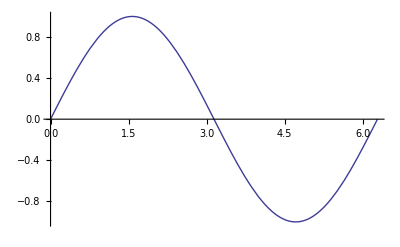

```mathematica
Plot[Sin[x],{x,0,2Pi}]
```

Note that the function to be plotted must  evaluate to a real number over the range of the plot.  No unknown constants can appear in the function. For instance, the function a x cannot be plotted vs. x unless the constant a has already been defined as some real number.

Also, functions that evaluate to complex numbers cannot be plotted (although one can plot the real and imaginary parts separately).

Forgetting these two simple facts is one of the most common sources of errors when making a plot. The error can be avoided by the following tactic: before you plot a function, evaluate it once at some arbitrary point. If unknown constants appear in the result, define them before continuing with the plot.

There are a large number of options available to modify the appearance of the plot. For example, to change the y-range of the plot from -2 to 2, add the following option PlotRange, as shown in Cell 9.71.

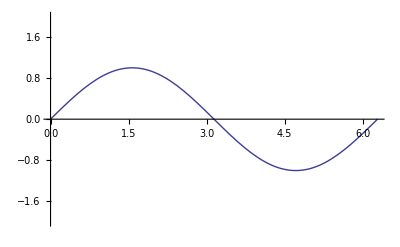

```mathematica
Plot[Sin[x],{x,0,2Pi},PlotRange->{-2,2}]
```

The arrow → in this cell was obtained by typing -> ("minus-greater than-space"). Mathematica automatically reformats this key sequence. Several other common symbols can also be created in this manner, such as ≤ (keyed as <= ), ≥ (keyed as >= ) and ≠ (keyed as != ).  Keyboard equivalents for many other symbols also exist; see Sec. 9.4.3.

Other options can be added as extra arguments to the function Plot. For example, to create axis labels and a plot label, use the options

AxesLabel → {"x","Sin[x]"}

PlotLabel → "A plot of Sin[x]"

One can also change the color of the lines in the plot, or change from solid to dashed or dotted lines. To change the color, use PlotStyle→RGBColor[r,g,b] where r, g, and b are real numbers between 0 and 1 giving the intensity of red, green and blue respectively.  For specific colors such as red, purple, green, etc, one can also use direct commands such as PlotStyle→Blue. To change to a dashed line, use the PlotStyle→Dashing[{line,space}], where line and space are the lengths of lines and spaces in the dashing. If you want to use both a colored and a dashed line,  make a list of PlotStyle options: for example,

PlotStyle →{RGBColor[1,0,0],Dashing[{0.05,0.05}]}

produces a bright red dashed line. The use of these and other options is illustrated in Cell 9.72. The Style command, used here to change the format of text in the plot, can sometimes be handy.

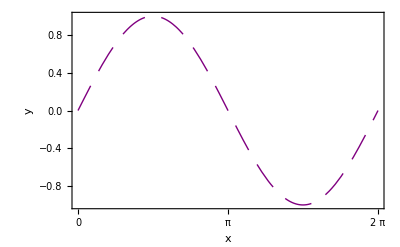

```mathematica
prettyplot=Plot[Sin[x],{x,0,2Pi},FrameTicks->{{0,Pi,2Pi},Automatic,None,Automatic},Frame->True,Axes->False, PlotStyle->{Purple,Dashing[{0.05,0.03}]},FrameLabel->{Style["x",FontFamily-> "Times",FontColor->Green,FontSize->18],"y","The Sine Function",""}]
```

Plots can  also be modified and examined using the drawing tools palette, available in the Graphics pull-down menu (or using the  ^T keyboard shortcut.) Using various tools in this palette, text and simple line drawings can be added to the plot. The x-y values of points  in the plot can also be read out by choosing the cursor tool and placing the mouse over the plot.

9.6.2 The Show Command

In order to show the same plot again but with new options, one can use the Show command. For example, to display the previous plot over a different range of x and y, use the command shown in Cell 9.73.

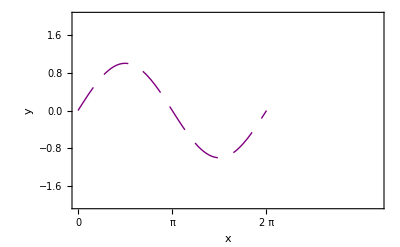

```mathematica
newplot = Show[prettyplot,PlotRange->{{0,10},{-2,2}}]
```

9.6.3 Plotting Several Curves on the Same Graph

More than one curve can be plotted at the same time using either Plot or Show. 
For example, to plot the cos and tanh functions over the same range of x, use the Plot command specifying a list of functions, {Cos[x],Tanh[x]}. Here's where it comes in handy to add colors and dashing in order to separate out the curves, as seen in Cell 9.74.

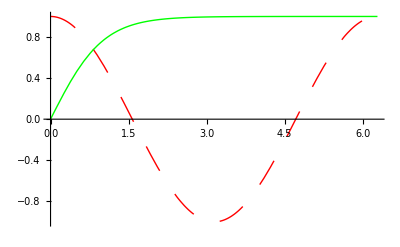

```mathematica
CTPlot = Plot[{Cos[x],Tanh[x]},{x,0,2Pi},PlotStyle->{{RGBColor[1,0,0],Dashing[{0.05,0.05}]},Green}]
```

The first element in the list of PlotStyle options in this cell, {RGBColor[1,0,0],Dashing[{0.05,0.05}]},  applies to the first function in the list of functions (i.e. Cos[x]). The second element, Green, applies to the second function Tanh[x].

One can also use the Directive command to group multiple style options for a single curve. In the above example, it is equally valid to use
PlotStyle → {Directive[Red, Dashing[{0.05, 0.05}]],Green}. There can be situations where grouping directives this way works  better than grouping directives as a list.

If you have already made two separate plots with two Plot commands, you can overlay them using the Show command.  For an example, see Cell 9.75.

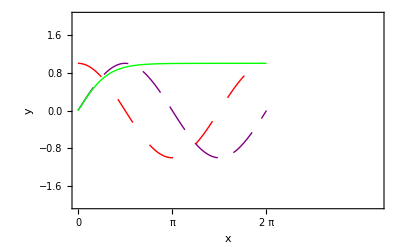

```mathematica
Show[newplot,CTPlot]
```

Note that the options chosen for the first plot take precedence over those of the second, determining the plot and axis labels and the range of x and y plotted.
	Plot and Show are summarized in Table 9.11.

Table9.11 Basic Plots
Plot[f,{x,xmin,xmax},option->value] | Plot f as a function ofx from xmin to xmax ,
and add an option
Plot[{f1,f2,,…},{x,xmin,xmax}] | Plot several functions on the same graph
Show[plot] | Redraw a plot
Show[plot1,plot2,…] | Show several plots

9.6.4 The ListPlot Function

Experimental data often comes in the form of lists of (x , y) positions. The ListPlot function is useful for plotting such data. To see an example, let's first artificially generate a list of data using the Table function:

```mathematica
data = Table[{i,Sqrt[i]},{i,0,10.,1.}]
```

{{0.,0.},{1.,1.},{2.,1.41421},{3.,1.73205},{4.,2.},{5.,2.23607},{6.,2.44949},{7.,2.64575},{8.,2.82843},{9.,3.},{10.,3.16228}}

We then plot the data using ListPlot, as shown in  Cell 9.77.

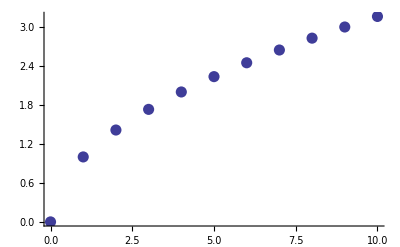

```mathematica
ListPlot[data,PlotStyle->PointSize[0.02]]
```

Note the use of a PlotStyle option here to make the size of the points larger. Another useful option is the 
Joined->True option, which joins points with line segments, as in Cell 9.78.

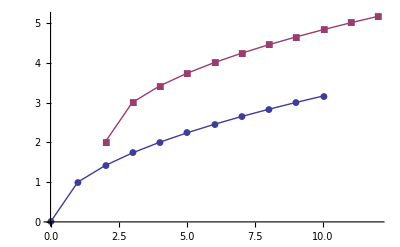

```mathematica
ListPlot[{data,data+2 },Joined->True,PlotMarkers->Automatic]
```

As you can see here, you can also plot several sets of data at a time using ListPlot. To get more than one dataset on the same plot, the syntax is  ListPlot[{data1, data2}].

9.6.5 Parametric Plots

Parametric plots are useful for plotting functions of a parameter.  For example, the position (x(t),y(t))  of a particle moving in two-dimensions is a function of  the parameter t, the time. The orbit of this particle in the x-y plane can be plotted using ParametricPlot, with the notation ParametricPlot[{x[t],y[t]},{t,a,b}], where a and b are the initial and final times.

For instance, consider the case of a two-dimensional harmonic oscillator. Here the position vs. time has the form (x_o cos(ω_x t), y_o sin(ω_y t + ϕ) ), where x_o and y_o are oscillation amplitudes in the x and y directions, ω_x and ω_y are the oscillator frequencies in the x and y directions, and ϕ is a phase.  ParametricPlot allows one to see the result of such an oscillation. In Cell 9.79,  we show an example with ϕ = 0, x_o = y_o = 1, ω_x = 2, ω_y = 6.

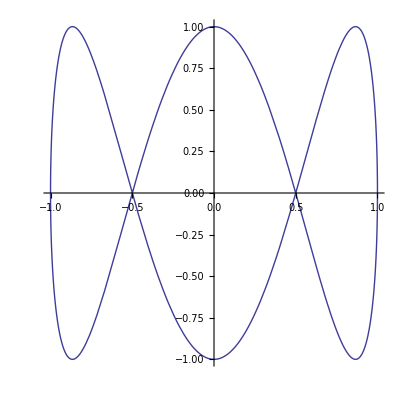

```mathematica
ParametricPlot[{Cos[2t],Sin[6 t]},{t,0,Pi},AspectRatio->1]
```

The result is a Lissajous figure. Note the use of an option, AspectRatio→1, which gives the plot the same dimension in x and y.

ParametricPlot also allows one to plot functions inpolar coordinates. To plot a function r(θ), where r is radius and θ is polar angle, write the (x,y) positions of this curve as(r(θ) cosθ,r(θ) sinθ). For example, a curve r(θ)=θ  is a spiral, as shown in Cell 9.80.

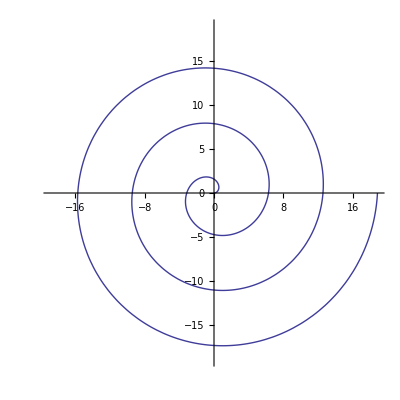

```mathematica
ParametricPlot[{θ Cos[θ],θ Sin[θ]},{θ,0,6 Pi},PlotRange->{{-6 Pi,6Pi},{-6Pi,6Pi}},AspectRatio->1]
```

ListPlot and ParametricPlot are summarized in Table 9.12.

Table9.12 Two Useful Types of x-y Plots

ListPlot[data] | Plot a list of x,y data of the form
 data={{x_1,y_1},{x_2,y_2},…}

ParametricPlot[{x[t],y[t]},{t,tmin,tmax}] | 
Plot y[t] vs. x[t]  as t varies from tmin to tmax

Many other types of plots are available, including plots with logarithmic axes, polar plots, etc. The syntax for such plots is similar to those discussed here. More information on different plotting options can be found in the Mathematica documentation.

9.6.6 3D Plots

There are various ways of plotting functions of two variables. One way is to make a surface plot. For example, to plot the surface z = sin(x y), use the Plot3D function. The basic form of this plot mirrors that of the Plot function, as shown in Cell 9.81.

```mathematica
plt = Plot3D[Sin[x y],{x,0,Pi},{y,0,Pi}]
```

-Graphics3D-

You can change the viewpoint of this plot by dragging on the plot with the mouse (try it with the above plot). You can zoom in or out using the mouse and holding down the option key. You can also change the viewpoint using a Show command, coupled with a ViewPoint option, as in

Show[plt, ViewPoint -> {0, 0, 3.000}]

(Try it!) The command ViewPoint->{0., 0., 3.} moves the (x,y,z) position of the viewpoint for the graph to the location (0,0,3) in "scaled coordinates", i.e. a point on the z axis, directly above the surface (see Mathematica help for more information).

Various other options can be added to surface plots. For example, the mesh used need not be the rectangular mesh shown above. The option MeshFunctions allows one to choose an arbitrary mesh on the surface, as shown below.   The syntax Function[{x,y},f[x,y]] is used here to define a "pure function" (a function without specific argument values)  whose contours determine the mesh. We will discuss pure functions in more detail later in the chapter, in Sec.  9.11.3.

```mathematica
Plot3D[Sin[x y],{x,0,Pi},{y,0,Pi},MeshFunctions->{Function[{x,y},Sin[x y]],Function[x,x^2]}]
```

-Graphics3D-

Another way to display information about a surface is to make a contour plot.  The function ContourPlot takes the same arguments as Plot3D, and displays 10 contours in grayscale, with lighter colours indicating higher areas of the surface, as in Cell 9.83.

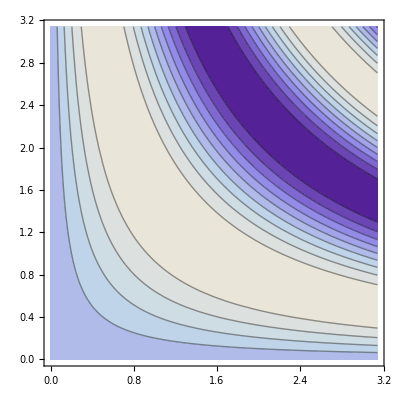

```mathematica
ContourPlot[Sin[x y ],{x,0,Pi},{y,0,Pi},PlotPoints->25]
```

We have used an option in this plot, PlotPoints → 25, in order to increase the initial number of points where the function has been sampled to a 25-by-25 grid (the default is 15-by-15).  For functions with rapid variation, this helps reduce errors in placement of the contours.

In this relatively basic version of a contour plot, the z-values of each contour are evenly spaced, but the spacing is determined automatically. To set the z-values by hand, use the Contours option, as in Contours→ {-0.9,-0.5,0,0.5,0.9}. This list gives the z-values where contours will be drawn. Alternatively, if one just wants to increase or decrease the number of contours, one can use Contours→ 30, which will now draw 30 evenly spaced contours.

By default, labels for contours have been added to this plot as "tooltips".  By placing your mouse over a contour, the contour height is then displayed. (Tooltips are a method for displaying information when the mouse passes over an object. See the Mathematica documentation for more information.) Labels for the contours can be permanently added to the plot using the option ContourLabels → True.

Table9.13  Two Ways to Plot Functions of Two Variables

Plot[f,{x,xmin,xmax},{y,ymin,ymax}] | Create a surface plot off as a function of x and y in the ranges
 xmin to xmax and ymin to ymax, respectively

ContourPlot[f,{x,xmin,xmax},{y,ymin,ymax}] | Create a contour plot of f as a function of x and y

9.6.7 Animations

There are several ways to make animations. For instance, you can create a sequence of plots of sin k x for different values of k using the Table command shown in Cell 9.84.

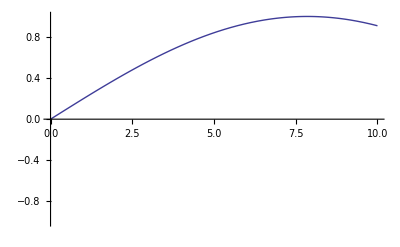
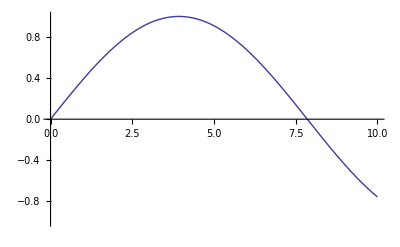
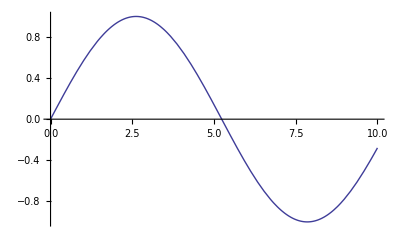
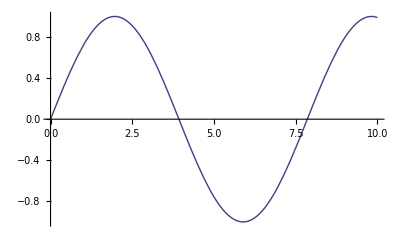
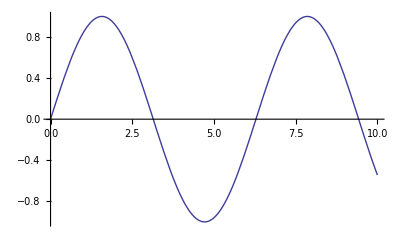
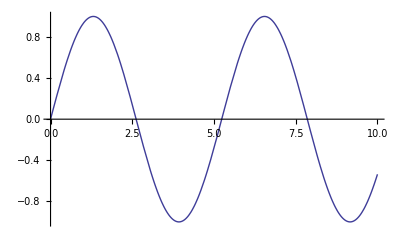
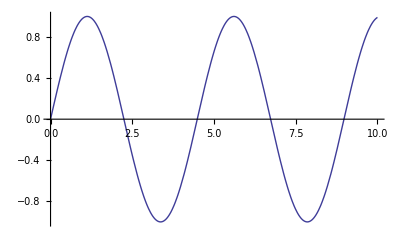
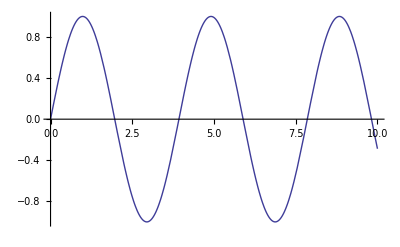

```mathematica
plottable=Table[Plot[Sin[k x],{x,0,10},PlotRange->{-1,1}],{k,.2,2,.2}]
```

To make an animation from this table of plots, you can use the ListAnimate command, which creates animations from any list of objects:

```mathematica
ListAnimate[plottable]
```

You can speed up or slow down the animation, run it forward or backward, or move through frames manually using the slider. If you don't want the animation to play automatically when you first evaluate the cell, you can add the option  AnimationRunning → False.

Also, as a general rule it is useful to specify the vertical range of the plots using the PlotRange option, so that the axes of the graphs remain fixed during the animation.

You can also create an animation more directly by using the command Animate, or alternately, Manipulate. Animate forms an animation from an expression by varying a parameter in the expression over time. The syntax is

Animate[expression, {k,kmin,kmax}]

or alternately,
		Animate[expression, {k,kmin,kmax,dk}]

to specify the step size in the parameter k.  Manipulate has the same syntax, but provides some other options in order to allow extra control over the result. An example of Animate is shown in Cell 9.87, and an example of Manipulate is shown in Cell 9.88.

```mathematica
f[k_,x_] = Sin[k x];
```

```mathematica
Animate[Plot[f[k,x],{x,0,10},PlotRange->{-1,1}],{k,.2,2,.2},AnimationRunning->False]
```

If you click the play button in the animation in Cell 9.87 you will see that it does not run properly until the function f(k,x) is evaluated (in Cell 9.86); whereas the animation in Cell 9.85 runs fine without any cell being evaluated. This is because the information required to make the animation in Cell 9.85 is already stored in the notebook as a table of plots; but the animation in Cell 9.87 is created "on the fly",  and the function f(k,x) being plotted must be evaluated before it can be animated.  In order to make  Cell 9.87 work without having to evaluate the function f(k,x)  every time the notebook is opened, you can add the option SaveDefinitions → True.  This is done in Cell 9.88 for the case of a Manipulate command. When such a cell is viewed, the function definitions required by the animation are then automatically evaluated.  This may be time-consuming if the evaluations are complex; in which case the ListAnimate method of animation may be superior. Also, be aware that the saved definitions are stored in the Global context along with other user-defined variables, as soon as the cell is viewed for the first time. These saved definitions may overwrite  or shadow previously-defined variables with the same name. For instance, without first evaluating Cell 9.88, you can check (using, for instance, ?g) that the act of viewing cell once causes the function g to be defined.

Since the option  SaveDefinitions → True can cause variables to be overwritten when the cell is viewed, I do not recommend using this method to store definitions in an animation. It is better to use a DynamicModule. This will be discussed in Chapter 4 in relation to Cell 4.7.

```mathematica
g[k_,x_] = Cos[k x];
Manipulate[Plot[g[k,x],{x,0,10},PlotRange->{-1.5,1.5}],{k,0,2},SaveDefinitions->True]
```

By clicking on the plus sign beside the slider in Cell 9.88 various controls are displayed, which allow one to step through or animate the plots.

Animate, ListAnimate, and Manipulate are examples of commands that create "dynamic content" in Mathematica notebooks.  Dynamic content runs automatically, without  requiring mouse clicks or other intercession by the user. This is a very powerful feature, and therefore must be treated carefully. It is possible for a hacker to code a Mathematica notebook with dynamic content that wipes out files or installs malicious software, without the knowledge of the user. Therefore, whenever you open a notebook with dynamic content, a dialogue box will appear asking if you wish to enable these features. You should only enable dynamic content in notebooks generated by trusted individuals or organizations.

There is a third way to create an animation that can sometimes be useful when the animation cells are very complicated. For slower computers this is currently the best animation method. First print out the series of cells to be animated using the Print command. Then by selecting these cells with the mouse, you can animate them by using the Animate Selected Graphics command under the Graphics -> Rendering menu. Here is  an example  using the same plots that were created in Cell 9.84:

```mathematica
Do[Print[plottable[[n]]],{n,1,Length[plottable]}];
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

The graphics cells are automatically grouped together, making it easy to select them all by clicking on the cell markers on the right hand side of the notebook window. Then by selecting the cells and clicking on Animate Selected Graphics, the cells are displayed one after another (try it). You may need to wait for a few moments while the cells are loaded into the Front End's memory, depending on the speed of your computer and the version of Mathematica. A control menu is also displayed in the lower left hand corner of the notebook. A mouse click anywhere in the notebook will stop the animation.

This animation method, as well the method using ListAnimate, does not need the kernel to be running in order to display the animation. However, Animate and Manipulate require a running kernel.

9.6.8 Add-On Packages, Contexts, and Shadowing

In addition to the many functions that are intrinsic to Mathematica, there are  other functions that are only available if you load in the appropriate add - on package into memory. These add - on packages are Mathematica notebooks that have within them the definitions of various functions. To extend the capabilities of Mathematica, there are a whole series of  add - on packages. Some of these functions will eventually become a part of the main Mathematica installation in future releases. For example, the current installation I am using (Mathematica 8.0) does not allow you to easily add legends to plots, but this capability is available in an add - on package. This package can be loaded into the kernel by typing <<PlotLegends`. (<<  is the notation used for loading external files. PlotLegends` is a context. Recall from Sec.  9.4.2 that a context is a "surname"  for a set of variables or functions.  In this case, the context refers to a collection of  functions and variables used in creating plot legends. All of the functions and variables in this context are loaded into memory when the command <<PlotLegends`is evaluated. )

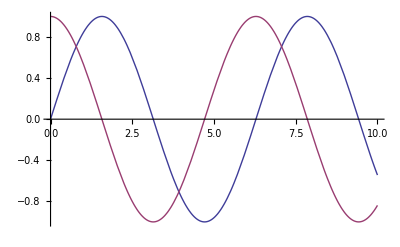

```mathematica
<<PlotLegends`

Plot[{Sin[x],Cos[x]},{x,0,10},PlotLegend->{Sin[x],Cos[x]},LegendPosition->{1.1,-.4}]
```

The options PlotLegend and LegendPosition have been used to label the different curves and determine the position of the legend.  These variables are only defined after the package PlotLegends has been loaded.  If you evaluate the above cell  before you have evaluated Cell 9.90 you will get an error because these options have not yet been defined.

The full name of these options is PlotLegends`PlotLegend and PlotLegends`LegendPosition. In other words, the context for these variables is PlotLegends. Several different contexts are generally in use in any given Mathematica session, and this has the following consequence. Two variables can have the same short name, but different contexts. For instance, if we remove the definitions in PlotLegends, we can create our own variable named LegendPosition, as in

```mathematica
Remove["PlotLegends`*"]

LegendPosition = 1;
```

The context for this variable can be found as follows:

```mathematica
Context[LegendPosition]
```

Global`

The Global context is the default context for user defined variables. However, if we reload the PlotLegends package, we will see a warning that there are now two variables named LegendPosition, but in different contexts:

```mathematica
<<PlotLegends`
```

LegendPosition::shdw: Symbol "LegendPosition" appears in multiple contexts {"PlotLegends`", "Global`"}; definitions in context "PlotLegends`" may shadow or be shadowed by other definitions.

The two variables named LegendPosition "shadow" one-another, i.e. one of them takes precedence over the other when only the short name is used. Variables that shadow one-another are displayed in Red to indicate that there is a potential problem.  For instance, if you now ask for the context of the variable LegendPosition you get a different answer than in Cell 9.92:

```mathematica
Context[LegendPosition]
```

PlotLegends`

This shows that the names of variables in the context PlotLegends take precedence over variables in the Global context. To determine the value of the user-defined variable LegendPosition you must type its full name:

```mathematica
Global`LegendPosition
```

1

Precedence between contexts is determined by order in the list $ContextPath, which lists the different contexts loaded in the current session:

```mathematica
$ContextPath
```

{PlotLegends`,PacletManager`,WebServices`,System`,Global`}

Here we see that variable names in the PlotLegends context take precedence even over system variables such as Pi.

In addition to the add-on packages that come with Mathematica, various external packages written by Mathematica users can be found on the world wide web. One particularly useful website in this regard is http://library.wolfram.com/database/MathSource/. There, you can find a large collection of notebooks that extend the capabilities of Mathematica.

(For more on loading external files, see the discussion of the Directory and SetDirectory commands in Sec. 9.11.4.)

Finally, Mathematica allows access to large databases over the internet.  For example, scientific and technical data,  and geographic data can be obtained using commands such as ElementData or CountryData. See the Mathematica documentation under the heading “Computable Data” for more information on how to use this constantly-updated source of information.

```mathematica
CountryData["China","Population"]
```

1.31436×10^9

Exercises for Sec. 9.6

(1) Using a plot, determine whether the equation 3 x^8-2x+1=0  has any real solutions. (Hint: Plot the left-hand side as a function of x and see whether it can equal zero for any real x.)

(2) A train pulls out of a station, with position x following the equation x = 0.1 t^2 as a function of time t. A second train coming into the station at high speed, sees the first train and applies its brakes, following the equation x = -20  + 5 t - t^2  - t^3 until it comes to a stop.  Use a plot to determine if the two trains collide.

(3) The solution of Newton's equations for the orbit of a mass point around a stationary mass (such as the sun) is defined in cylindrical coordinates (r,θ) by the equation 1/r=1/r_o(e sinθ+1)  where the orbit parameters r_o and e (e being the orbit's eccentricity) are both greater than or equal to zero. Taking e =0,1/2,1, and 2, for each case

(a) Plot r/r_o as a function of θ using a polar plot. Classify each orbit as an ellipse, a parabola, or a hyperbola.

(b) In each case find the value of   r/r_o and  θ  for  perihelion (closest approach to the sun).

(4) The power density S (energy released per unit volume per unit time) in an industrial process is found empirically to depend on the mean density n  of fuel in the reactor , and the temperature T according to  S=0.04(n^3.2+0.2 n^0.7 T^1.3 ⅇ^(T^2/100))/(10+T^2)   kW/cm^3, (where T  and n are measured in units of 100 K and 1 g/cm^3 respectively) .  Furthermore, if the power density exceeds S = 1 kW/cm^3, the power release will exceed cooling capacity , the temperature will increase, and the reactor will melt down. Use a contour plot to find the regime  of safe operation in  n and T.

(5) Create an animation of the function defined by r^2(θ,t)= θ+t, where (r,θ) are polar coordinates. This curve is related to Fermat's Spiral. Plot the function in the x-y plane with -5<x<5,-5<y<5, for -t<θ<10π,  and animate it at a sequence of times from 0≤ t≤ 1.8π, in units of 0.2 π.

(6) Read about the plotting function ParametricPlot3D in the Mathematica documentation. Use this function to create a surface plot in Cartesian coordinates (x,y,z) of a Möbius strip (a surface with only a single side),  defined in cylindrical coordinates (r,θ,z) by the parametric equations r(s,θ)=  1 + s cos(θ/2), z(s,θ)=s sin(θ/2), -1/2<s<1/2, 0<θ<2 π .  (You can put more twists in the strip by replacing θ/2 with n θ/2.)

(7) Read about the plotting function ContourPlot3D. Use this function to plot the surface defined by the equation f(x,y,z) = 0, where f(x,y,z) =x y^2- y z^2 + z x^2  , over the range -3 to 3 in each dimension. Use the mouse to view the surface from all sides, and determine where there is a singularity.

## 9.7 Help for Mathematica Users

By now you can see that there's a lot to remember--and we are just getting started! Fortunately, Mathematica  comes with an excellent online help facility. It is available on the main menu under Help. If you go to it now, and  type into the search window  the name of an intrinsic function that you wish to learn about, the documentation will display information about the function, including options, examples, and information about other related functions. Also, the function index in the help browser has an alphabetical list of every function.

The examples displayed in the help window can be modified and evaluated, just like the examples in the electronic version of this textbook,  allowing you to easily explore variations in the examples.

You can also find information about Mathematica functions directly within a Mathematica session. In order to see the definition of a function, type ?Function. For example,

```mathematica
?Eigenvalues
```

RowBox[{"Eigenvalues", "[", StyleBox["m", "TI"], "]"}] gives a list of the eigenvalues of the square matrix StyleBox["m", "TI"]. 
RowBox[{"Eigenvalues", "[", RowBox[{"{", RowBox[{StyleBox["m", "TI"], ",", StyleBox["a", "TI"]}], "}"}], "]"}] gives the generalized eigenvalues of StyleBox["m", "TI"] with respect to StyleBox["a", "TI"]. 
RowBox[{"Eigenvalues", "[", RowBox[{StyleBox["m", "TI"], ",", StyleBox["k", "TI"]}], "]"}] gives the first StyleBox["k", "TI"] eigenvalues of StyleBox["m", "TI"]. 
RowBox[{"Eigenvalues", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["m", "TI"], ",", StyleBox["a", "TI"]}], "}"}], ",", StyleBox["k", "TI"]}], "]"}] gives the first StyleBox["k", "TI"] generalized eigenvalues.

This also works for user-defined variables and functions. For instance, if you define a function  as

```mathematica
f[x_] = x Sin[x];
```

you can check its definition using

```mathematica
?f
```

Global`f

f[x_]=x Sin[x]

The first line is the full name of the variable, including its context. You can also obtain a list of all user-defined variables that have been employed in the current session:

```mathematica
?Global`*
```

By clicking on the symbols, you will obtain their definitions and/or values.  Eigenvalues is not listed, because it is not a user-defined variable; and x is listed because it was used, even though it has not yet been given a definition.

To see all of the options available for any Mathematica function,  you can  type ??Function or Options[Function]. For example, typing  ??Plot results in a long list of options for the plot command, as well as the values they take by default.

You may also have noticed that Mathematica automatically colors symbols  to aid in formatting input. Brackets are colored pink until they are closed, as are trailing commas or unfinished operators such as /.→ .  Grey is used for text strings. When the kernel is running, dark blue is used for variables that have not yet been defined in the current session. Black is used for variables that have been previously defined, including intrinsic functions.  Blue-green is used for dummy variables such as function arguments, or iterators in tables and sums. Red is used for syntax errors. Also, Mathematica places a red caret below locations where it expects more input. For instance, if you forget to type the second required argument in an intrinsic function the caret will appear. If you evaluate the command anyway, error messages typically result. Even though these messages are sometimes cryptic, you should read them carefully as they contain useful clues that will help you correct the error:

```mathematica
Plot[x^2,]
```

Plot::pllim: Range specification Null is not of the form {x, xmin, xmax}.

Plot[x^2,Null]

Here, the error message tells us that we need extra input of the form {x, xmin, xmax}. Null is the term Mathematica uses for the absence of an expression or variable.

Finally, another aid to users has been incorporated into Mathematica 8.0: the WolframAlpha “computational knowledge engine”. For computers connected to the internet this allows, among other things, relaxed “free-form” syntax (i.e. plain English) in Mathematica commands. The commands are interpreted using the  computational knowledge engine rather than the kernel, provided that they begin with an equal sign “=” .  You can pose all sorts of questions to the computational engine this way, without requiring correct syntax. For instance,  you can have Mathematica plot sin(x) by simply typing “= plot sin x” over any given range:

WolframAlphaQueryResults

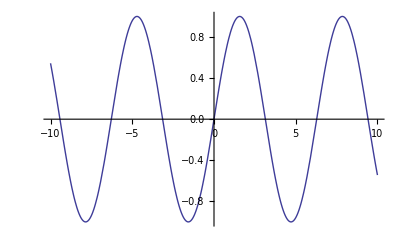

The computational engine can also access a broad range of databases, from economics to astrophysics. One can pose questions like:

WolframAlphaQueryResults

174.2 GeV/c^2

or

WolframAlphaQueryResults

7.72 million  (2009 estimate)

Note that extra information can often be obtained by clicking on the plus sign in the upper right corner of the pane.

English sentences are obviously easier to use than Mathematica syntax (although for complicated expressions they are not always interpreted properly). However, the WolframAlpha interpretation is (usually) provided in exact Mathematica syntax, so as to reduce misunderstanding.

In this book we will not resort to relaxed syntax, preferring instead to employ exact Mathematica syntax. However, you might find relaxed syntax useful in various circumstances, such as for hints in remembering the exact syntax for a given operation such as plotting or root finding.

## 9.8 Computer Algebra

9.8.1 Manipulating Expressions

Mathematica can do symbolic as well as numerical mathematics.  The program will perform basic algebraic simplifications automatically, as in

```mathematica
4x+5-3x+15
```

20+x

However, Mathematica will not expand out expressions in brackets unless you ask it to do so using the Expand function:

```mathematica
5(x+2y) +10(x -4y^2 x-y)
```

5 (x+2 y)+10 (x-y-4 x y^2)

```mathematica
Expand[%]
```

15 x-40 x y^2

Another way to simplify an expression is to apply the Factor command, which tries to factor out all common elements in an expression. For example, when applied to the above result,  Factor yields

```mathematica
Factor[%]
```

-5 x (-3+8 y^2)

There are also several command that are useful when  dealing with  complex expressions that include terms with numerators and denominators. For instance,  the expression

```mathematica
x/(x^2 + 2) + 3/(x-1)
```

3/(-1+x)+x/(2+x^2)

can be put over a common denominator, using the function Together:

```mathematica
Together[%]
```

(6-x+4 x^2)/((-1+x) (2+x^2))

The numerator and denominator of the expression can then be extracted using the functions Numerator and Denominator:

```mathematica
Numerator[%]

Denominator[%%]
```

6-x+4 x^2

(-1+x) (2+x^2)

If you really want Mathematica  to do all of the work (and after all, isn't that what computers are for?), the function Simplify will try various tricks to simplify a given expression . The function FullSimplify has an even larger bag of tricks,  but for this reason takes somewhat longer  to run. For example, Simplify knows all the trigonometric identities:

```mathematica
Simplify[ Sin[x]^2 Cos[x]+ Cos[x]^3]
```

Cos[x]

One of the palettes, called AlgebraicManipulation, contains a  suite of functions that are useful in simplifying or otherwise manipulating algebraic expressions. A list of some of these commands is also provided in Table 9.14.

Table9.14Some Useful Functions for Doing Computer Algebra
Expand[expr] | Multiply out products and powers
Factor[expr] | Reduce to a product of factors
Together[expr] | Put all terms over a common denominator
Apart[expr] | Separate out into terms with simple denominators
Simplify[expr] | Try to simplify an expression
FullSimplify[expr] | Try a larger collection of tricks to simplify an expression
Numerator[expr] | Pick out the numerator of an expression
Denominator[expr] | Pick out the denominator of an expression

9.8.2 Replacement

In order to evaluate an expression at specific values of the variables that appear in the expression, you can perform a replacement. For example, to evaluate the expression x^2 at x=2, you can replace the variable x  by 2 using the notation

```mathematica
x^2 /.x->2
```

4

The symbol  /.  can be thought of as the verb "replace", and the expression /. x →2  means replace x with 2. The right arrow →  can be obtained from the BasicInput palette, or by typing ->   ("minus-greater than-space"). You can perform more than one substitution at the same time by using a list after the symbol /.:

```mathematica
y Cos[x] /.{x->45 Degree, y->2}
```

√2

The use of this command is summarized in Table 9.15.

Table9.15 Performing  Substitutions in an Expression
expr /.x  →value | Replace x with value everywhere in the expression expr
 expr/.{x  →xval,y  →yval ,…} | Perform several replacements at once

9.8.3 Defining Functions

## Functions of One Variable

If you need to evaluate an expression like x^2+2x+3 many times at different values of the variable, you can save typing in all those /. and →  symbols by creating your own function, f(x) = x^2+2x+3. Then to evaluate the function at x=2 you need only type f[2].  To define this function type

```mathematica
f[x_] = x^2+2x+3
```

3+2 x+x^2

You can now evaluate this function for any value of x:

```mathematica
f[2]
```

11

The underscore in the definition of f(x) is very important. The notation x_  means the following: treat x as a stand-in for any number, variable, or expression. To understand what this implies, let's see what happens if we leave out the underscore, defining a new function g(x) as

```mathematica
g[x] = x^2
```

x^2

Then if we ask for the value of g at some point, we obtain the following:

```mathematica
g[2]
```

g[2]

Typing  g[2] just returns g[2] rather than 4, because g[2] has not been defined. We have not defined g(x) for any x. Rather, g(x) is defined only when the argument is x itself, and no other quantity.  The underscore in x_   tells Mathematica, "when I type x here, I don't literally mean just x,  I mean  any variable, number, or expression".

This distinction between g[x] and g[x_] seems like splitting hairs, but it can actually be useful. For example, say you want to define a function h(x) that equals x^2 everywhere except at a specific point x=a, where you want the function to be 0.  Then  type

```mathematica
h[a] = 0;

h[x_] = x^2;
```

Evaluating the function at x=3  yields the correct result:

```mathematica
h[3]
```

9

Also, evaluating the function at the special point x=a yields

```mathematica
h[a]
```

0

## Checking the Definition of a Function

If you want to check the definition of a user-defined function, type ?functionname, just as you would for an intrinsinc function. For example, to check the definition of our function h(x), type

```mathematica
?h
```

Global`h

h[a]=0
 
h[x_]=x^2

Function definitions valid only at specific points like x=a always supersede the more general definitions created by placeholders like x_.This is why the general definition h[x_]=x^2 does not apply to h[a].

## Functions of Several Variables

Creating  a function with more than one argument is a straightforward generalization of the previous syntax. For instance, to define a function p(x,y) = y sin x,  type

```mathematica
p[x_,y_] = y Sin[x];
p[60 Degree,2]
```

√3

Table9.16 Defining Functions
f[x]=expr | Define the function f at the value x(and only at x)
f[x_]=expr | Define the function f for any value of x
?f | Ask for the definition of a function

9.8.4 Applying Functions

Mathematica allows you to apply functions to their argument(s) in several ways. For example, to evaluate f(x), you can type

f[x]
x//f
f@x

All three forms have their uses. For example, recall that we applied the second form of notation to numerical evaluations in Sec. 9.1 when we used x//N rather than N[x].  This "afterthought" form is useful when you have typed out a long expression and then decide to apply a function to it.  The "forethought" form f@x will not be used much in this book, but does correspond to the theoretical picture of a function f "acting on" a variable x.

For functions of two arguments, such as p(x,y) above, you can use the notation x~p~y. An example of notation of this type is the + symbol. x+y in Mathematica actually stands for x ~Plus~ y, where Plus[x,y] is the addition function. In fact, one of the basic ideas behind Mathematica is that any mathematical operation can be thought of  as a function acting on arguments.

9.8.5 Delayed Evaluation of Functions

Sometimes a function can't be evaluated by Mathematica until a specific value of the argument is given. For instance, this happens when you deal with functions that require specific numerical inputs. Say, for example, that you wish to define a function f(x) that plots the function sin y on the interval -x<y<x. To do so you might type

```mathematica
f[x_] = Plot[Sin[y], {y, -x, x}]
```

Plot::plln: Limiting value -x in {y, -x, x} is not a machine-size real number.

Plot[Sin[y],{y,-x,x}]

However, as you can see, that won’t work. Remember from Sec. 9.1 what the = sign means: it means, evaluate the right-hand side and assign the result to the symbol on the left-hand side. Here, however, the right-hand side cannot be evaluated, because no particular numerical value for x has been specified.

To get around this problem, you must use a different type of equal sign, := , which means "delayed equal". With this delayed equal sign, Mathematica remembers that a function has been defined, but does not evaluate the right-hand side until the function is actually called.

Using delayed evaluation allows us to define f(x) as

```mathematica
f[x_] := Plot[Sin[y],{y,-x,x}]
```

There is no result plotted because there has been no evaluation of the right-hand side yet.  However, if we now ask for f at a particular value of x, Mathematica recalls the definition and performs the evaluation, as shown in Cell 9.127.

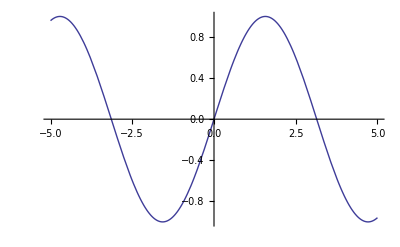

```mathematica
f[5]
```

The distinction between = and :=  is summarized in Table 9.17.

Table9.17 The Difference Between  = and :=
f[x_]=expr | immediately evaluate expr and define f[x]
f[x_]:= expr | remember this definition of f, but do not evaluate expr until f[x]  is used

9.8.6 Putting Conditions on Function Definitions

Special procedures are necessary when defining discontinuous functions. For example, consider the Heaviside step  function

h(x)={0
1 , x<0
, x> 0

In order to create a user-defined version of this function in Mathematica,  condition statements can be used:

```mathematica
h[x_] := 1 /; x>0
h[x_] := 0 /; x<0
```

The symbol /; means "on condition that" and is followed by logical statements limiting the range of validity of the definition. Note that we have used  delayed equal signs :=  in the definitions, because the conditions cannot be evaluated until specific values of x are chosen.

Also, note that we have not defined h(x) at x=0. Normally that doesn't matter, but in Mathematica you will not get a numerical result if you evaluate h(0). So it is probably best to define h(0), taking, say, h(0) = 1/2:

```mathematica
h[0] = 1/2
```

1/2

You can now evaluate h(x) anywhere on the real line. (What do you think would happen if you evaluated h(x) at a complex number?) In Cell 9.130 we plot the function (with a slightly thickened line for ease of viewing).

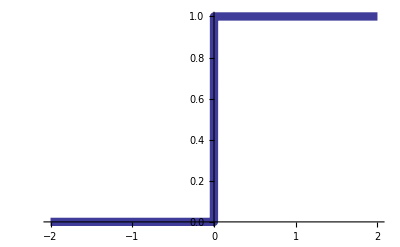

```mathematica
Plot[h[x],{x,-2,2},PlotStyle->Thickness[0.015]]
```

Table 9.18 summarized some of the conditions one can add to function definitions.

Table9.18 Adding Conditions to Function Definitions

f[x_]:=expr /;conditions | Adds conditions to the definition of a function

some possible conditions:
x==y | Test whether x equals y
x ≠y | Test whether x is unequal to y
x >y | Test whether x is greater than y
x ≥y | Test whether x is greater than or equal to y
x < y   | Test whether x is less than y
x ≤y | Test whether x is less than or equal to y
condition_1&&condition_2 | Test whether both condition_1 and condition_2 are true
condition_1||condition_2 | Test whether either condition_1 or condition_2 is true

The conditions in Table 9.18 are also referred to as logical statements. Logical statements are either true or false. For instance, if x=1 and y=0, the statement x==y returns False:

```mathematica
x=1; y=0;
x==y
```

False

We will see later that logical expressions are used in many other ways, such as in the control of computer programs.

A second way to add conditions to function definitions is to use Piecewise. A function defined by Piecewise[{{val1,cond1},{val2,cond2},...}] takes the value val1 when condition cond1 is met, val2 when condition cond2 is met, and so on. A function defined using Piecewise can often be integrated and differentiated using Mathematica when the same function defined using the /; notation cannot (see the next section on Calculus).  
	For example, the previous step function can also be defined as

```mathematica
Clear[h];
h[x_] = Piecewise[{{1,x>0},{0,x<0},{1/2,x==0}}]
```

Piecewise[{{1, x>0}, {0, x<0}, {1/2, x==0}, {0, True}}]

Exercises for Sec. 9.8

(1) Use Mathematica to help prove the following trigonometric identities:

(a)  2 cos^4(x)+2 sin^4(x)+sin^2(2 x)=2.

(b) (sec(x)-csc(x))/(cot(x)+tan(x))=(tan(x)-cot(x))/(csc(x)+sec(x)).

(c)  (2 sin(2 x)-sin(4 x))/(cos(x))=8 sin^3(x).

(2) Factor the following polynomials:

(a) x^3+3 x^2-4.

(b) x^5+5 x^4+10 x^3+10 x^2+5 x+1.

(c)  x^6+3 x^5-21 x^4-59 x^3+96 x^2+276 x+144.

(3) Simplify the following equation using Mathematica, and use the result to find all real and complex solutions by hand:

1/30+4/(21 (3 z-1))-3/(26 (2 z+1))-41/(455 (5 z-4))=0.

(4) Use a substitution command to evaluate the following functions at the specified values of the variables:

(a) sin x + sin(2x)+ sin(3x)+sin(4x)…+sin(10 x) at x=20 °.

(b) x^2 + 2 x y + y^2  at x=1, y=-1.

(c) x^2  - y^2 at x=coshθ, y=sinhθ. (Simplify the result.)

(5) Define the following functions and, if asked,  plot them over the given range of values:

(a)  f(x)=x/(x^2+1). Plot over -3<x<3.

(b) f(x,y)=tanh(x/y) .  Plot with a surface plot over -1<x<1, -1<y<1. What is happening along the line y=0?

(c) f(x)=  dimension of the vector x.  Evaluate for x  = (2,4,3,2), and x=(1,-1).

(d) f(x) = Piecewise[{{x,, x<0}, {x^2,
1/x^2,, 0≤ x≤ 1
x>1}}]      Plot for -3<x<3.

## 9.9 Calculus

9.9.1 Derivatives

You can take the derivative of an expression using the intrinsic function D. This function takes two arguments: D[expr, var] is the derivative of the expression expr with respect to the variable var. For example, D[f[x],x] means ⅆf/ⅆx.

For instance,  if we define the function f(x)=tan(x^2), Mathematica will evaluate the derivative with respect to x, using the chain rule:

```mathematica
f[x_] = Tan[x^2];
D[f[x],x]
```

2 x Sec[x^2]^2

Another way to evaluate the derivative is to use a prime ', as in f'[x]:

```mathematica
f'[x]
```

2 x Sec[x^2]^2

Multiple derivatives can be taken by adding more primes:

```mathematica
f''[x]
```

2 Sec[x^2]^2+8 x^2 Sec[x^2]^2 Tan[x^2]

or by using the notation D[f[x],{x,n}], where n is the order of the derivative:

```mathematica
D[f[x],{x,4}]
```

96 x^2 Sec[x^2]^4+24 Sec[x^2]^2 Tan[x^2]+256 x^4 Sec[x^2]^4 Tan[x^2]+192 x^2 Sec[x^2]^2 Tan[x^2]^2+128 x^4 Sec[x^2]^2 Tan[x^2]^3

The derivative of a function is the function's slope. One sometimes needs to find extrema of functions, which are places where the slope is zero ( ⅆf /ⅆx = 0). You can do this in Mathematica  by taking the derivative, and then manipulating the resulting expression to simplify it. For example, to find the extrema of x^2/(1-x+x^2),  type the following:

```mathematica
D[x^2/(1-x+x^2),x]
```

-(x^2 (-1+2 x))/((1-x+x^2)^2)+(2 x)/(1-x+x^2)

To see where the zeros of this function lie, you can simplify it via

```mathematica
Factor[%]
```

-((-2+x) x)/((1-x+x^2)^2)

One can now see that the extrema are at x=0 and at x=2.

When evaluating the derivative of  a  function of several variables,  the derivative should be interpreted as a partial derivative.  For example,

D[g[x,y],x] means  ∂g/∂x|_y,

the derivative of g with respect to x, holding y fixed.

9.9.2 Power Series

The power series of a function f(x), taken with respect to a point x=a, is a polynomial approximation to the function that  matches the value of the function and its derivatives at the given  point a:

f(x)≃f(a)+(x-a)f'(a)+1/2(x-a)^2 f''(a)+...+1/(n!)(x-a)^n(ⅆ^n f)/(ⅆ x^n)|_(x=a)+... .

Equation (9.9.1) is also called a Taylor series for the function f(x) about the point a. The "approximately equal to" sign ≃ is used here because in general the expression works well only for x near a.  Even if the series keeps an infinite number of terms, it may not evaluate to f(x) for all x, or may not even be defined.

For example,  taking the series of x^(3/2) around x=0 produces a series that has undefined terms beyond the first. Using Eq. (9.9.1), we have

x^(3/2) ≃0+x·0 + 1/2 x^2·∞+...

This series is practically useless, because the function x^(3/2) has a singular second derivative at the point x=0 where we are performing the expansion.

Nevertheless, for smooth functions power series can be very useful approximations . To create a power series with M terms about the point x=a of an expression expr , the syntax is
	Series[expr,{x,a,M}]
For instance, a four-term power series for √(x+1)  about x=0 is given by

```mathematica
s=Series[Sqrt[x+1],{x,0,4}]
```

1+x/2-x^2/8+x^3/16-(5 x^4)/128+O[x]^5

The resulting approximation to √(x+1)  is a special Mathematica object, a Series, which can be seen by the O[x]^5 at the end of the expression. This indicates the order of the approximation: there is an error between the series and  √x of the order of magnitude x^5. In other words, if we reduce the value of x by a factor of 2, the error in the above series approximation is reduced by a factor of 2^5 (for x sufficiently close to 0).

Any  function that  is added to a series expression will automatically be expanded in a series to the same order of approximation. For example,  adding 1/(x+4) to this series results in a new series which is an approximation to  √(x+1)+ 1/(x+4) :

```mathematica
1/(x+4) + s
```

5/4+(7 x)/16-(7 x^2)/64+(15 x^3)/256-(39 x^4)/1024+O[x]^5

Since Series are special objects, they cannot be directly evaluated at particular values of x. If you try, you will get an error:

```mathematica
s/.x->2
```

SeriesData::ssdn: Attempt to evaluate a series at the number 2. Returning Indeterminate.

Indeterminate

In order to evaluate the series at a particular value of x, it must first be transformed from a series expression back to a normal expression with the command Normal:

```mathematica
Normal[s]
```

1+x/2-x^2/8+x^3/16-(5 x^4)/128

This approximation to √(x+1)  can now be evaluated. For example, in Cell 9.143 we plot it and compare it to the original function √(x+1).

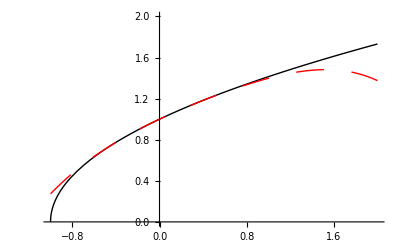

```mathematica
Plot[{Sqrt[x+1],%},{x,-1,2},PlotRange->{0,2},PlotStyle->{RGBColor[0,0,0],{RGBColor[1,0,0],Dashing[{0.05,0.05}]}}]
```

The power series expansion about x=0, shown as a dashed line, works quite well provided that x is not too different from 0.  By keeping more terms in the series, you can convince yourself that the power series  will only converge to the right answer if |x|<r,  where r is the radius of convergence of the series. For this example, one can show that r=1, so the power series only works in the range -1<x<1. This is because √(x+1) has a singularity at x=-1, and this singularity cannot be well-represented by a polynomial expansion.

Actually, Series can perform expansions that are more general than the simple polynomial Taylor series of Eq. (9.9.1). For example,  expanding the function √(1/x^(2/3)+ 1)  about x=0 (where there is a singularity) yields the following non-polynomial expression:

```mathematica
Series[Sqrt[1/x^(2/3)+1],{x,0,3}]
```

1/x^(1/3)+x^(1/3)/2-x/8+x^(5/3)/16-(5 x^(7/3))/128+(7 x^3)/256+O[x]^(11/3)

9.9.3 Integration

Mathematica can perform symbolic integration.  In order to evaluate the indefinite integral ∫f(x)ⅆx of a function f(x), use the notation Integrate[f[x],x]. The second argument gives the variable over which the first argument is integrated. For example, the indefinite integral  of the hyperbolic tangent is

```mathematica
Integrate[Tanh[x],x]
```

Log[Cosh[x]]

You can verify this result by taking its derivative:

```mathematica
D[%,x]
```

Tanh[x]

To evaluate definite integrals, you need only specify the range of integration along with the integration variable. For example,  to evaluate the integral of cos^2 x from 0 to 2π, use

```mathematica
Integrate[Cos[x]^2,{x,0,2 Pi}]
```

π

Mathematica is generally very careful when evaluating integrals to make sure that they converge properly. When there is a question as to the existence of the result, Mathematica  will often supply ranges of free parameters in the integrand for which the integral exists. For example, Mathematica recognizes that  ∫_0^∞ 1/(x^a+1)ⅆx exists only if Re a>1:

```mathematica
Integrate[1/(1 + x^a),{x,0,Infinity}]
```

ConditionalExpression[(π Csc[π/a])/a,Re[a]>1]

Here, we encounter a conditional statement for the first time. This statement takes two arguments: ConditionalExpression[result, logical expression]. That is, the first argument is returned if logical expression is true. If it is false the result is undefined (new in Mathematica 8.0 -- in previous versions, an If statement was employed here).  In other words, if we substitute a →  -1, then Mathematica  can't find the integral and it returns the symbol Undefined . However, for a >0 the second argument is returned:

```mathematica
%/.a->-1

%%/.a->7
```

Undefined

1/7 π Csc[π/7]

Note that errors in Mathematica's integral evaluations crop up from time to time, so it is always best to carefully check your results. For instance, this integral was not properly evaluated in Mathematica 7.0 , but the error has been corrected in Mathematica 8.0.

Of course, there are many convergent integrals for which there is no analytic answer in terms of pre-defined functions. A simple example is

```mathematica
Integrate[Exp[-Exp[x^2]],{x,0,Infinity}]
```

∫_0^∞ ⅇ^(-ⅇ^(x^2))ⅆx

However, Mathematica can evaluate integrals like this numerically, as we will discuss in Sec. 9.11.

Table 9.19 Calculus in Mathematica
D[f,x] | The (partial) derivative of f with respect to x
Integrate[f,x] | The (indefinite) integral off with respect to x
Integrate[f,{x,xmin,xmax}] | The definite integral of f from xmin to xmax
Series[f,{x,x_o,n}] | The power series of order n for f with respect to x around x_o
Normal[series] | Convert a power series into a normal expression
Limit[f,x→ x_o] | Take the limit of f as x approaches x_o

Exercises for Sec. 9.9

(1) Find all local extrema of the following polynomial:  x^4+5 x^3-3 x^2+2.

(2) Find all local extrema of the following function of x and y, and classify these extrema as either minima, maxima or saddlepoints: 
			 f(x,y)=y x^2+y^2 x-2 x(y+2).

Find the value of the function at each extremum. (Hint: A high-resolution contour plot is helpful. )

(3) Find the following indefinite integrals, and prove by differentiating the result that Mathematica did the integral properly. (Some of the results may be in terms of special functions, whose definitions need not concern you at this time. You may need to manipulate the results in order to return them to their original form after differentiating the integrals.)

(a)  ∫x^3/(sin^2(x))ⅆx.

(b) ∫x^a log^3(x)ⅆx.

(c)  ∫ⅇ^(-x^3)ⅆx.

(4) Evaluate the following definite integrals:

(a) ∫_(-∞)^∞ (cos(p x))/(a^2+x^2)ⅆx , assuming that p  and a are real.

(b) ∫_0^(2 π) cos(z sin(x))ⅆx , assuming that z is real.

(c)  ∫_0^∞ x ⅇ^(-x^4)ⅆx.

(5) Find the power series expansion to 6th order around x=0 of the function f(x)=(x+1)ln(x+1) . Plot the resulting series on the same graph as f(x) for -1<x<2. Repeat for the 100th-order series. Can you tell from these plots what is the radius of convergence of this power series?

(6) A particle moves in one dimension. Its velocity as a function of time is given by the function   v(t)=-4 t^3+t^2+1, where t is measured in seconds.

(a) Find and plot the particle's position x(t) for 0<t<2 seconds, assuming that the particle is at x=-1 at t=0.

(b) Find the maximum positive excursion, x_max.

7(a) Assuming that the particle in Exercise (6) has a mass of 5 kg, plot the total force F(t) on the particle for 0<t<2 seconds.

(b) Find the work done by the force as a function of time,  W(t)=∫_0^t F(t) v(t)ⅆt.

(c) Show that for this particle the work W(t) equals the change in kinetic energy of the particle ΔK=1/2 m[(v(t))^2-(v(0))^2]:

W(t) = ΔK(t),

(This is called the work-kinetic-energy theorem.)

## 9.10 Analytic Solution of Algebraic Equations

9.10.1 Solve and NSolve

## One Equation in a Single Variable

Say you want to find the solution for x to an equation such as  f(x) = 0. If an analytic solution exists, Mathematica can usually find it using the Solve function. The syntax for this function is as follows:

Solve[f[x]== 0,x]

The first argument is the equation to be solved,  and the second argument is the variable x which is being solved for.

Note the double equal signs in the equation f[x]== 0.  Here we encounter yet another meaning of "equals". In this case, the equation f[x]== 0  expresses a question: is the left-hand side f(x)  equal to the right-hand side 0? It is called a logical statement because the result is either True or False. For example, the statement 1 == 0  will return False; and the statement Simplify[(x+1)^2 == x^2 + 2x + 1] yields True. (Try it!) You have seen logical statements before: in Sec. 9.8.6 they were used to place conditions on function definitions

If  you were to use a single equal sign to define the equation f(x) = 0, you would be assigning the value 0 to the function f when its argument takes on the value x, which is not what we want to do here.

As a simple example of the function Solve, let's find the roots of the cubic polynomial x^3 + 2 x^2 -x - 2. To do so type and evaluate

```mathematica
Solve[x^3 + 2 x^2 - x -2==0,x]
```

{{x→-2},{x→-1},{x→1}}

The result is the three solutions for x, written as a list of replacements. You can check that these are in fact the solutions by substituting the list back into the polynomial:

```mathematica
x^3 + 2 x^2 - x - 2 /.%
```

{0,0,0}

While analytic solutions to cubic and even quartic polynomials can be found, solutions to higher order polynmials can usually only be found numerically. Nevertheless, Mathematica will take a stab, returning some strange-looking stuff:

```mathematica
Solve[x^5 + x^2 + 1 ==0,x]
```

{{x→Root[1+#1^2+#1^5&,1]},{x→Root[1+#1^2+#1^5&,2]},{x→Root[1+#1^2+#1^5&,3]},{x→Root[1+#1^2+#1^5&,4]},{x→Root[1+#1^2+#1^5&,5]}}

What we have here is a list of numerical values for the solutions, found using a Mathematica function called Root whose specialty is polynomial root finding. (The Solve function calls Root when it recognizes a polynomial equation.) In this form the result is not much use to anyone, but you can get numerical values for the roots by applying the N function to this list:

```mathematica
N[%]
```

{{x→-1.19386},{x→-0.15459-0.828074 ⅈ},{x→-0.15459+0.828074 ⅈ},{x→0.751519-0.784616 ⅈ},{x→0.751519+0.784616 ⅈ}}

Alternatively, you can avoid the weird intermediate stuff by using the function NSolve[f[x]== 0,x], which basically stands for N[Solve[f[x]==0,x]].  This takes you directly to the numerical form of the solution:

```mathematica
NSolve[x^5 + x^2 + 1 ==0,x]
```

{{x→-1.19386},{x→-0.15459-0.828074 ⅈ},{x→-0.15459+0.828074 ⅈ},{x→0.751519-0.784616 ⅈ},{x→0.751519+0.784616 ⅈ}}

## Coupled Equations in Several Variables

Solve and NSolve can also be used to solve coupled systems of equations. Now the arguments are

Solve[{eqns},{vars}]

where {eqns} is a list of equations, and {vars} is the list of variables to be solved for. For example,  the coupled system of linear equations

x+y+z=0, 						
z+2y=4, 						
z+3=2,

has the following solution:

```mathematica
Solve[{x+y+z==0,x+2y == 4,z+3==2},{x,y,z}]
```

{{x→-2,y→3,z→-1}}

Tip: if you forget to use the double equal sign, and instead use a single equal sign, remember that you have now assigned the right-hand side to the left-hand side. Sometimes Mathematica will not allow such an assignment, as in  x+3=y. (Try it: you will get an error.) However, if your equation takes a form such as x=y-3, Mathematica will assign y-3 to x.  Now the result of evaluating  x==y-3 will  be the logical result True, because Mathematica substitutes for the value of x. To stop this from happening,  you need to clear the value of x  using Remove[x] or Clear[x].

As another example of coupled equations, consider a system of masses connected by springs. Such systems are often used to model the behavior of elastic materials. For instance, the compression of an elastic rod standing on its end on a table can be modeled by a system of M+1 one-dimensional coupled harmonic oscillators at positions y=y_i. The first mass is at y=y_0=0, and the location of subsequent masses is determined by the force balance equations

0=-k(y_i-y_(i-1))+k(y_(i+1)-y_i)- m g, i=1,2,3,...M-1.

The last mass, at the top of the chain, has no mass above it,  so its equilibrium equation is different:

0=-k(y_M-y_(M-1)-a) - m g,

where a is the equilibrium displacement between the masses in the absence of gravity.

You can use Solve to determine the equilibrium positions of the masses in such a system.  First,  choose a value of M and define the position of the lowest mass, sitting at y=0:

```mathematica
M=20;
y[0] = 0;
```

Next,  make a table of equations for the other masses, i=1,..,M-1

```mathematica
eqns = Table[0==-(2y[i]-y[i-1]-y[i+1])- m g/k,{i,1,M-1}];
```

To this list you must add the equation for the last mass:

```mathematica
eqns = Append[ eqns,0==-(y[M]-y[M-1]- a )- m g/k];
```

Finally,  define the list of variables, and solve the equations:

```mathematica
vars = Table[y[i],{i,1,M}];
soln = Solve[eqns, vars];
```

Although we suppressed the output in order to save space, you can check that Mathematica actually solved the coupled equations analytically. For more complicated problems, it is usually better to solve the problem numerically, providing values for the parameters in the equations before a solution is attempted.

In Cell 9.161 we plot the positions of the masses using a ListPlot, taking g=9.8 , m=0.1,k=10, a = 0.2:

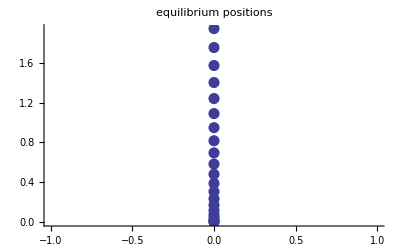

```mathematica
g=9.8;m=0.01;k=10;a=0.2;
pos = Table[{0,y[i]},{i,0,M}]/.soln[[1]];
ListPlot[pos,PlotStyle->PointSize[0.02],PlotLabel->"equilibrium positions",Axes->{False,True}]
```

The rod is compressed near the bottom because of the weight of the masses above it. The reader is invited to vary the parameters in this problem, to answer the following questions:

How does the overall height of the rod depend on the combination m g/k? How does it depend on a?  How does it depend on the number of masses M? (For this simple system, these questions can also be easily addressed analytically. Some examples in the exercises are given for which  the answers are not quite so obvious.)

## Linear Equations and Under-Determined Systems

Note that the equations (9.10.1) are linear, and so can be written as a matrix equation

L·(x,y,z)=(0,4,2-3)=(0,4,-1),

where L=(1 | 1 | 1
0 | 2 | 1
0 | 0 | 1).This matrix has a nonzero determinant, and therefore a unique solution can be found by the matrix inversion technique discussed in Sec. 9.5. Consider, however, the case of a matrix with zero determinant, such as the matrix g  that appeared in Eq. (9.5.10). Matrix inversion does not work for such a matrix, because when the determinant of g is zero, a solution need not exist, and if it exists it will not be unique. Nevertheless, one can apply Solve to the system to find the solution(s), if any:

```mathematica
g={{1,2,3},{2,4,6},{3,6,9}};
Solve[g.{x,y,z}=={1,1,1},{x,y,z}]
```

{}

In this case, no solution exists because the three equations are self-contradictory.  However, for other equations involving g there can be an infinite number of solutions (the system is under-determined):

```mathematica
Solve[g.{x,y,z}=={1,2,3},{x,y,z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x→1-2 y-3 z}}

Now  the three equations for x, y, and z are identical and so there are more unknowns than there are independent equations,  leading to a range of possible values for x, y,  and z.

## Nonlinear Equations

There are many nonlinear equations with perfectly good solutions that can't be found analytically using Solve, or numerically using NSolve. Solve and NSolve only work on certain simple types of equations like polynomial equations or linear equations. An example where both Solve and NSolve fail is the equation

cos x= ⅇ^x.

If you try to solve this equation using Solve or NSolve you will get an error:

```mathematica
Solve[Cos[x] == Exp[x],x]
NSolve[Cos[x] == Exp[x],x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[Cos[x]==ⅇ^x,x]

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[Cos[x]==ⅇ^x,x]

In the next section, we will consider numerical methods for solving general nonlinear equations.

Table 9.20  Three different Types  of Equations
x=y | Immediately evaluate y and assign result to x
x:=y | Evaluate and assign y to x  only after x  is evaluated
x==y | Test whether x and y are equal

Table9.21 Solving Equations for All Roots, Analytically and Numerically

Solve[lhs==rhs,x] | Solve an equation,giving a list of replacements for x 
x /. solution | Use the list of replacements to get values for x

NSolve[lhs==rhs,x]
or
N[Solve[lhs==rhs,x]] | 

Solve certain simple types of equations numerically

Exercises for Sec. 9.10

(1) Figure 9.4 shows several masses suspended in equilibrium from a mobile, with the length ratios of the crossbars shown. Assuming that the crossbars and strings have negligible mass, that mass 1 is 2 kg, and mass 6 is 1 kg,  find the values for the unknown masses m_2,m_3,…m_5. (Hint: Recall that in equilibrium the torques from each weight must balance: torque = perpendicular force × lever arm length.) Use a pencil and paper to set up this problem. Don't try to do everything at the keyboard!

Fig. 9.4

(2) Find the current I_1 running through resistor R_1 in the circuit of Fig. 9.5 :

Fig. 9.5

where V_1 = 12V, V_2 = 8V, R_1 = 20Ω, R_2 = 15Ω, R_3 = 3Ω, R_4 = 6Ω, R_5 = 12Ω,  and R_6 = 2 Ω. 
(3) Solve the following coupled equations analytically, finding all solutions (real and complex):

x^2+2 y=0,

y^2+2 x=0

Find numerical values for the solutions.

(4) An elastic band is  fixed between posts a distance L apart in the horizontal (x) direction. A simple model for the deformation of the band in the presence of gravity is as a system of equal masses m coupled by springs, each with spring constant k. In the absence of gravity, the masses are at positions r_i=(i a ,0), i=0,1,2,...,M, where a=L/M.The  first and last mass in the chain are fixed at r_o={0,0} and r_M={L,0}.  In between the masses are located according to the force-balance equations

(0,0)=- k(r_i-r_(i-1))+k(r_(i+1)-r_i)-m g (0,1)

Find and plot the shape of the band in equilibrium by solving for the positions of the masses and creating a ListPlot. Solve for the case M=30, m=k=a=1 and g=1/50. (Hint: Solve can handle vector equations of the form {0,0}= 2 r_i -r_(i-1)-r_(i+1)+(m g/k)  (0,1) without having to break the equation up into components However, the variables to be solved for cannot be vectors. Instead, define r[i]={x[i],y[i]}, and create a list of variables {x[i],y[i]}using a Table command. (Be sure to Flatten the table, so that the list is in the right format to be used in Solve.)

(5) A rod or plate differs from the elastic band model used in the previous problem in that atoms in a rod are stacked in crystal planes, and repel one-another if they are too closely-spaced.  These two effects, which were not included in the previous problem, provide added strength against external shearing forces on the rod.  Here we will determine the effect of gravity on a horizontal rod. The rod consists of two horizontal layers of atoms whose positions are given, in the absence of gravity, by  R_i= (i-1) p+Mod[i,2] q , i=1,2,3,...,M, where p=a(1/2,0) and  q=a(0, √(3/2)). The rod is shown in Cell 9.165, taking M=81and a=1/4 (i.e. L=10):

```mathematica
Clear["Global`*"]; M=81;a=1/4;
```

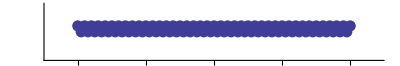

```mathematica
p=a{1/2,0}; q=a{0,Sqrt[3]/2};
R[i_] = (i-1) p + Mod[i,2] q;
ListPlot[Table[R[i],{i,1,M}],PlotStyle->PointSize[0.02],PlotRange->{{-1,11},{-1,1}},AspectRatio->1/6,Ticks->{Automatic,None}]
```

The first two and last two masses in the rod are assumed to be attached to walls, so only the masses with 3≤ i≤ M-2 are allowed to move. All the masses are assumed to interact via a simple nearest-neighbor interaction. For neighbors i and j separated by displacement vector r, we assume that the force between them is F=-k_(i j)(r-a r̂), where k_(i j) is the spring constant:

```mathematica
F[i_,j_ ,r_] := -k[i,j](r - a r/√(r.r))
```

This is an isotropic spring force with a resting length a, so that in equilibrium the atoms are spaced by a, in the absence of other forces. However, this force is nonlinear in the displacement r, since the unit vector r̂=r/√(r·r). Solve will not be able to find a solution for force equilibrium for the fully-nonlinear equations. Therefore, we assume that the atoms are only slightly displaced from equilibrium, and Taylor-expand the force about the equilibrium positions R_i to obtain linear equations in the displacement from the force-free equilibrium. That is , we write r_i= R_i+  (Δx_i, Δy_i), and Taylor expand F(r_i-r_j) for small  (Δx_i, Δy_i). This is accomplished below, and the result is called δF(i,j):

```mathematica
r[i_] = R[i] + λ{Δx[i],Δy[i]};
δF[i_,j_] = Simplify[Normal[Series[F[i,j,r[i]-r[j]],{λ,0,1}]]/.λ->1];
```

The total force on the i th atom F_tot(i) , assuming that this atom is not at the ends,  is due to its four nearest neighbors (one on each side in the same row, and the two nearest atoms along diagonals in the other row):

F_tot(i)=(0,-m g) + δF (i,i-2)+δF (i,i-1) +δF(i,i+1) + δF (i,i+2) , for  3≤ i ≤ M-2.

```mathematica
Ftot[i_] := {0,-m g} +   δF[i,i-2]+δF[i,i-1] +δF[i,i+1] + δF[i,i+2]  /; 3≤ i≤ M-2
```

The masses on the ends are fixed to the walls, so

```mathematica
Δx[i_]:=0 /; i==1 ||i==2||i==M-1||i==M
Δy[i_]:=0 /; i==1 ||i==2||i==M-1||i==M
```

(a) Solve the coupled equilibrium equations F_tot(i)={0,0} for the variables (Δx_i, Δy_i), i=3,...,M-2, and plot the shape of the rod. (Hint: Create a table of the equations, and a list of variables. Apply Flatten to the tables to remove internal brackets in the lists, so that the syntax matches that required in Solve. Assume that the ends of the rod are clamped, so that (Δx,Δy)=(0,0) for the end masses. ) Take m=k_(i j)=1, and g=5. × 10^-5.

(b) Plot the maximum vertical displacement of the rod,  max [|Δy|], vs. g by choosing five  g-values in the range 0≤ g≤ 10^-4.

(c) Plot max [|Δy|] vs. M for g=5. × 10^-5,  m=1,  a=1/4,  and k=1. Take M=10,20,30,40. (This changes the length of the rod without affecting its intensive properties such as elasticity). How does the maximum sag scale with the length of the rod?

(d) Plot the shape of the rod for the same parameters as in part (a), but now assume that one of the springs has failed, so that

(i) k_(10, 11)=k_(11,10)=0 (break between atoms 10 and 11 in the top and bottom rows).

(ii) k_(10, 12)=k_(12,10)=0 (break within the same row).

The large difference between these two cases points out the importance to the shear strength of  the diagonal interactions between atoms in different layers . These interactions provide a cantilever effect : the diagonal springs are compressed or stretched as the rod sags, providing a restoring force that is  missing when there is only one row, or when a diagonal spring is broken.  [See Exercise (1), Sec. 1.5) for an analytic treatment of this problem.]

(6) Repeat Exercise (5) for a rod that is clamped horizontally to a wall only at the left end, with the other end free to sag in gravity. Plot the shape of the rod for M=40, k=1,m=1, a=1/4, and g=5× 10^-6 , and determine how the maximum sag scales with the length of the rod for M=10,20,30,40. [See Exercise (7)(c), Sec. 4.2, for the analytic solution to this problem.]

(7) A  linear model of a solid two-dimensional pyramid consists of the following coupled mass-spring system. The masses have equilibrium  positions shown in Cell 9.171, given by the equations R_(i j)= i p+j q, i=0,1,2,...10 and j=0,1,2,...10-i, where p=(1,0) and q=(1/2, √(3/2)). However, they are subjected to gravity, and therefore the pyramid compresses under its own weight; see Fig. 9.6.

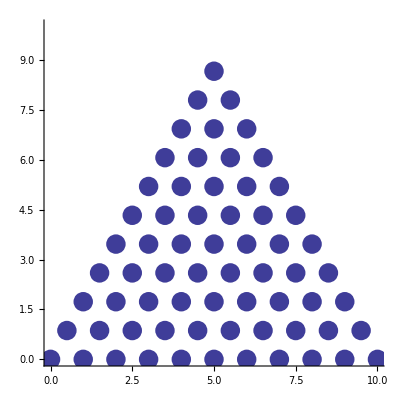

```mathematica
p={1,0}; q={1/2, Sqrt[3]/2};
R[i_,j_] = i p + j q;
ListPlot[Flatten[Table[Table[R[i,j],{j,0,10-i}],{i,0,10}],1],PlotStyle->PointSize[0.035],PlotRange->{{0,10},{0,10}},AspectRatio->1]
```

(a)For m=k=1 and g=0.2 find the equilibrium shape, assuming that the masses in the base are fixed, by solving for the equilibrium position of the masses using the same spring force as in the previous problem with interior masses connected to their 6 nearest neighbors, and linearizing the equations in small displacements from equilibrium. (The solution is shown in Fig. 9.6 for g=0.1. )

Fig. 9.6 Solution for g=0.1.

(b) Plot how the height of the pyramid depends on g over the range -0.2<g<0.2, for m=k=1.

## 9.11 Numerical Analysis

In this section, we examine a few of the elementary numerical procedures commonly used by scientists and engineers: numerical solution of algebraic equations, numerical integration, interpolation, and fitting.  In university courses on numerical methods it was once de rigeur to spend a considerable amount of time discussing the theory behind these procedures. However, hardly anyone writes their own codes to perform these tasks anymore.   Here, we focus on the Mathematica intrinsic functions that perform these operations. Some of the basic techniques, such as Newton's method and least-squares fitting, are considered in the exercises.

9.11.1 Numerical Solution of Algebraic Equations

In order to solve the equation f(x) = 0 numerically,  it is often a good idea to plot the function f(x) in order to see whether solutions exist for real x.  Take, for example,  f(x) = cos(x) - ⅇ^x.  A plot of this function is shown in Cell 9.172.

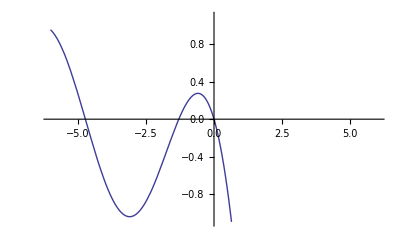

```mathematica
Plot[Cos[x]-Exp[x],{x,-6,6},PlotRange->{-1.1,1.1}]
```

You can see that there are in fact several solutions. One is at x=0, and there are others at x<0.  In order to find a numerical approximation to any one of these solutions, use the function FindRoot. This syntax for this function is 
FindRoot[eqn,{var,guess}],where eqn is the equation being solved ( f[x]==0 in this example),  var  is the variable being solved for (x in this case), and  guess is an initial guess for the value of x that solves the equation. (Note the double equal sign syntax in the equation f[x]==0 , just as in the intrinsic functions Solve and NSolve.) FindRoot will then attempt to find the solution closest to the given initial guess.  For example, if you choose for our initial guess x=-2, you obtain the following result:

```mathematica
FindRoot[Cos[x] -Exp[x]==0,{x,-2}]
```

{x→-1.2927}

FindRoot uses Newton's method to quickly obtain the solution. It is not particularly important to understand how Newton's method works (some programming ideas are needed to explain it: see the Exercises).  However, it is important to know how well the solution works. We can find out by substituting it back into the function cos x- exp x:

```mathematica
Cos[x] - Exp[x] /.%
```

5.55112×10^-17

There is a very small error, as expected in any numerical solution. But the accuracy is  as high as one can expect to achieve in a computer system where $MachinePrecision is 16, ie. 16-digit numerical precision. The accuracy of the solution can be adjusted by using several options.  AccuracyGoal  is an option that sets the wished-for number of digits of accuracy in both the position of the root, and the value of the function at the root.   PrecisionGoal specifies the wished-for number of digits of accuracy in the position of the root only. WorkingPrecision specifies the numerical precision to be used in the internal computations. The default settings for  AccuracyGoal and PrecisionGoal are WorkingPrecision/2. amd the default setting for WorkingPrecision is $MachinePrecision. Mathematica will perform the rootfinding to arbitrary precision, depending on the value of WorkingPrecision.   For instance,

```mathematica
FindRoot[Cos[x] -Exp[x]==0,{x,-2,-2.1},WorkingPrecision->100]
```

{x→-1.29269571937339838116818912159060704947302123097024791883636929497994337420582584433210669099139032}

This solution is more accurate than the previous solution:

```mathematica
Cos[x]-Exp[x]/.%
```

-1.00187752×10^-90

Note that two initial guesses were used in Cell 9.175. This option allows root finding on a function without taking its derivative (using a variant of the secant method). This can be useful in applications where such derivatives are not defined. We will see examples of such functions in coming chapters (for instance, Chapter 1, Cell 1.77).

To find another solution, you must supply another guess. FindRoot only finds one solution at a time:

```mathematica
FindRoot[Cos[x]-Exp[x],{x,-5}]
```

{x→-4.72129}

There are also complex solutions to this equation, and FindRoot will find them if an appropriate initial guess is supplied:

```mathematica
FindRoot[Cos[x] - Exp[x],{x,3 + 3 I}]
```

{x→2.79508+3.48751 ⅈ}

When using FindRoot, it is important to remember that no unknown constants can appear in the equation : after all, we are performing a numerical solution so only numbers can appear in the equation.

For example, the equation a x + b=0  has a perfectly good analytic solution x=-b/a,  but FindRoot will not work unless specific numerical values for a and b are given:

```mathematica
FindRoot[a x + b ==0,{x,1}]
```

FindRoot::nlnum: The function value {1.` a + b} is not a list of numbers with dimensions {1} at {x} = {1.`}.

FindRoot[a x+b==0,{x,1}]

FindRoot can also  find a numerical solution to coupled equations in several variables. For example, the coupled equations

cos(x y)+y ⅇ^x=0
 y^2-y+x=0

have the following solution:

```mathematica
FindRoot[{Cos[x y]+ y Exp[x] ==0,y^2 - y + x ==0},{x,1},{y,-1}]
```

{x→-1.61481,y→-0.86558}

This is only one of several solutions. To find these other solutions, you need guesses that are close to the exact solutions. Such guesses can be made only if you know something about the functions. The following graphical method is useful in this regard: Plot the zero of each equation separately in the x-y plane using  a ContourPlot; then superimpose the zeros to find solutions to the coupled system.

The solution to cos(x y)+y ⅇ^x=0 is a set of curves y(x) in the (x,y)- plane, which can be determined by asking for the zero contour of the function cos(x y)+y ⅇ^x, as shown in Cell 9.181.

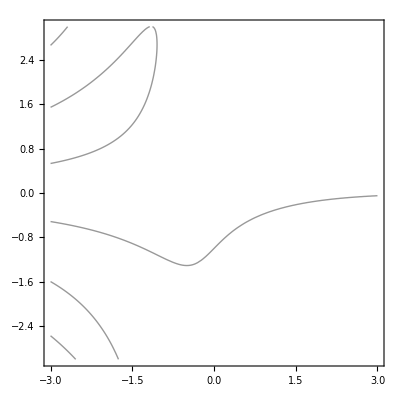

```mathematica
ContourPlot[Cos[x y] + y Exp[x],{x,-3,3},{y,-3,3},Contours->{0},PlotPoints->40,ContourShading-> False]
```

We have turned off contour shading so that only the zero contour  is shown.

To find solutions to the coupled equations (9.11.1) you must now plot the zero contour of the  function in the second equation,  x + y^2 - y  (see Cell 9.182; this time we plot the contour as a thick red line to distinguish it from the first set of curves):

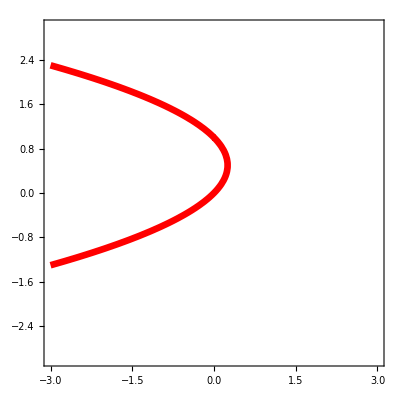

```mathematica
ContourPlot[x+y^2 - y==0,{x,-3,3},{y,-3,3},PlotPoints->40,ContourShading-> False,ContourStyle-> {RGBColor[1,0,0],Thickness[0.012]}]
```

Here we have used the somewhat simpler notation f[x,y]==0 in the first argument of ContourPlot to find the zero contour. Finally, by superimposing the two plots, we can find simultaneous solutions to both equations, as shown in Cell 9.183.

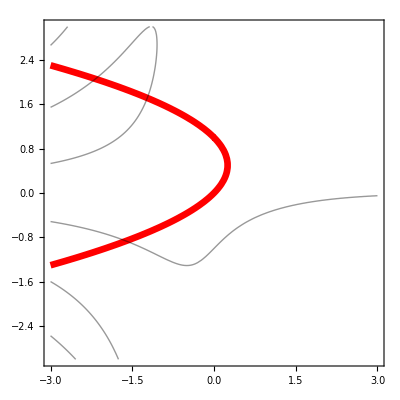

```mathematica
Show[%,%%]
```

The crossing points of the thin and thick curves show where both equations are satisfied, and are our solution points. The crossing point in the lower left quadrant is the one that was found by FindRoot previously.  Now that we know roughly where other solutions lie in the x-y plane, we can choose initial guesses close to each one to find these solutions. For example:

```mathematica
FindRoot[{Cos[x y]+ y Exp[x] ==0,y^2 - y + x ==0},{x,-2},{y,2}]
```

{x→-2.17578,y→2.05749}

Unfortunately, there is no general algorithm for finding all of the numerical solutions at once to general nonlinear equations. One needs to supply a guess for each solution, and this requires extra work, like the plotting we did in the above examples.   This is one of the reasons why complete analytic solutions of nonlinear systems (if such solutions are available) are superior to numerical solutions.

Syntax for the command FindRoot is summarized in Table 9.22.

Table9.22 Finding One Numerical Solution of an Equation

FindRoot[lhs==rhs,{x,x_o}]  | Find a single numerical solution to an equation, given an initial guess
 (only if lhs and rhs have analytic derivatives wrt x)
FindRoot[lhs==rhs,{x,x_o,x_1}] | Find a numerical solution to an equation, given two initial guesses 
(required if lhs or rhs do not have defined derivatives )

9.11.2 Numerical Integration

We saw in Sec. 9.9.3 that some definite integrals cannot be evaluated analytically. These integrals can be evaluated numerically using NIntegrate. The syntax for this function is identical to that for a definite integral. For example, to numerically compute ∫_0^∞ ⅇ^(-ⅇ^(x^2))ⅆx , one might type

```mathematica
NIntegrate[Exp[-Exp[x^2]],{x,0,Infinity}]
```

0.2633

This function goes to zero so rapidly at large x that it is sufficient to ask for the integral from 0<x<5:

```mathematica
NIntegrate[Exp[-Exp[x^2]],{x,0,5}]-%
```

9.61176×10^-13

Since this is a numerical method, it is important to be able to test the accuracy. This can be accomplished by asking for more precision in the integral, via the PrecisionGoal option. This option sets the number of digits of precision of the integral relative to the magnitude of the integral. By varying PrecisionGoal we can see the integral's value converge :

```mathematica
Table[InputForm[NIntegrate[Exp[-Exp[x^2]],{x,0,5},PrecisionGoal->n,MaxRecursion->50]],{n,3,15}]
```

{0.2633001925783607,0.2633001925783607,0.26330018327243604,0.26330018327243604,0.26330018327200766,0.26330018327201044,0.26330018327201044,0.26330018327201044,0.26330018327201044,0.26330018327201044,0.26330018327201027,0.26330018327201027,0.26330018327201027}

Here the InputForm  (see Sec. 9.2.6)  is displayed in order to view the full precision of the numbers. Note that the integral's value is often of higher precision that what was requested. The option MaxRecursion has  been set to 50 so that a sufficient number of bisections of the interval (0,5) can be taken in order to achieve the requested accuracy. The  default setting for MaxRecursion is 7 and for PrecisionGoal it is WorkingPrecision/2. Just as for the FindRoot command , the default value of WorkingPrecision is $MachinePrecision. If even higher precision is required, you can increase the value of WorkingPrecision, as we did previously when working with FindRoot (see Cell 9.175).Thus, numerical integrals can be found to arbitrarily high accuracy.

9.11.3 Interpolation

Given a list of (x,y) data, it is often useful to be able to define a function f(x) that goes through each point  (x,y) in a fashion that is as smooth as possible. One can then treat this function like any other function in Mathematica, taking its derivative or finding its zeros, for example.

To create this function from a data set, use the Interpolation command. As an example, we will first create some (x,y) data, then apply Interpolation to the data. The data will be points taken from the function y=x^5 on -1<x<1:

```mathematica
data=Table[{x,x^5},{x,-1,1,0.05}];
f=Interpolation[data]
```

InterpolatingFunction[{{-1.,1.}},<>]

The result of the interpolation is something called an InterpolatingFunction, which we assigned to the variable f.  The first argument of this InterpolatingFunction is {{-1.,1.}}. This is the range of x values over which the function is defined (in this case from -1 to 1 , because this was the range of the data). The second argument <> denotes an argument that is hidden from view; it is a long list of numbers used to define this function.

However, there is no argument in the InterpolatingFunction that allows you to evaluate the function at a given value of x. This type of object is called a pure function in the nomenclature of Mathematica. To use it,  simply add an argument to it. In other words,  f is a function (a pure function), and f(x) is the value of that function at position x:

```mathematica
f[0.7]
f[-0.3]
```

0.16807

-0.00243

You can plot f(x) (Cell 9.191), or take its derivative (Cell 9.192), just as you would any other function (in its range of validity)

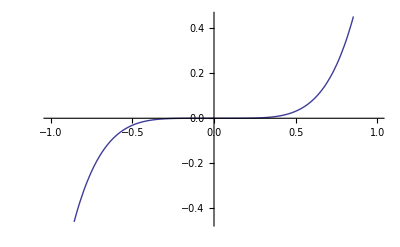

```mathematica
Plot[f[x],{x,-1,1}]
```

```mathematica
f'[0.2]
```

0.008225

The interpolating function is guaranteed to equal the original data at the given data points, and connects the data points "as smoothly as possible".  In more detail, what this means is that the interpolating function consists of a set of cubic polynomials. Each polynomial in the set is applied only between two corresponding consecutive data points.  The polynomials are "spliced together" at each data point  to form a function that  is continuous and has continuous first and second derivatives. (The  hidden argument in the interpolating function is a list of the coefficients in this set of polynomials.) This type of interpolation is commonly called a cubic spline interpolation. General spline fits can allow the fitting function to be multi-valued (i.e. several values of y are possible for a given value of x, as in a circle), but the implementation used in Mathematica  assumes a single-valued function. For this reason, the data must be such that no two x values are the same. For fitting multi-valued data, use SplineFit, available in the add-on package Splines. Here is an example:

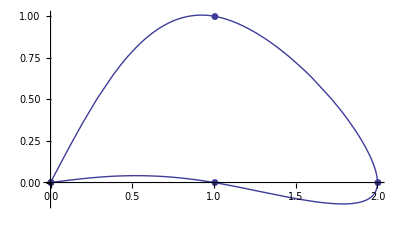

```mathematica
<<Splines`
multivalueddata={{0,0},{1,0},{2,0},{1,1},{0,0}};
fm = SplineFit[multivalueddata,Cubic];
ParametricPlot[fm[s],{s,0,5}];
ListPlot[multivalueddata,PlotMarkers->Automatic];
Show[%%,%]
```

In a cubic spline interpolation the third derivative will not be continuous in general, as you can see in Cell 9.193.

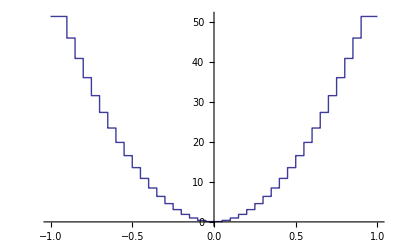

```mathematica
Plot[Evaluate[f'''[x]],{x,-1,1},PlotPoints->300]
```

You can ask that higher-order (or lower-order) polynomials be used in the fitting, by choosing the option InterpolationOrder→  n,  where n is the order of the polynomials. This is necessary if  third or higher-order derivatives of the interpolated data are required. An example is given in Cell 9.194.

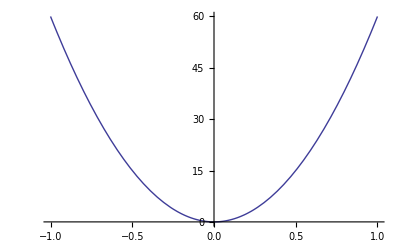

```mathematica
f=Interpolation[data,InterpolationOrder->5];
Plot[f'''[x],{x,-1,1}]
```

9.11.4 Fitting

It is sometimes necessary to find a function that fits given data as closely as possible. This can be accomplished with Mathematica's Fit function. The Fit function will fit a particular functional form to the data. The functional form is taken from  a list of functions provided by the user, such as {1,x,x^2,x^3}. Fit takes the data itself as its first argument, and this list of functions as the second argument. The third argument is the variable(s) used in the fit. In other words,  the proper syntax is Fit[data,function list,vars]. Fit then finds the best linear combination of functions appearing in function list in order to fit the data.  For example, Fit[data,{1,x,x^2,x^3},x] tries fits of the form a + b x + c x^2 + d x^3 . Here’s an example using the data created in Cell 9.188:

```mathematica
Fit[data,{1,x,x^2,x^3,x^4,x^5},x]
```

-9.53632×10^-17-4.1031×10^-16 x+6.64904×10^-16 x^2+0. x^3-7.56685×10^-16 x^4+1. x^5

Fit has done a very good job reproducing the original function, x^5, from the data set. All the terms except for the x^5 term have negligibly small coefficients.

Fits to functional forms that do not involve simple linear combinations of functions can also be performed. The function FindFit  can make such fits: see the help browser for more information.

Table9.23 Numerical Operations on Data Sets

Interpolation[data] | Create a numerical interpolating function that
interpolates a data set by trying to smoothly go 
through each data point
InterpolatingFunction[{xmin,xmax},<>][x] | Evaluate an interpolating function at
position x,xmin <x <xmax
Fit[data,function list,vars] | Fit data with a linear combination
of functions,each function taken
from function list

## Reading Data from External Files

Mathematica has several intrinsic functions that can be used to import data.  First, you must place a file containing the data in one of the directories on your computer where Mathematica looks for files. The list of these directories is held in the variable $Path. The current working directory is a member of this list, and it can be determined using the command

```mathematica
Directory[]
```

/Users/dubin

(In Mathematica versions previous to 4.1, the  directory is specified using colons to denote subdirectories rather than the above backslash notation.) You can change the current working directory using the SetDirectory command.  For instance, to access files on my computer in a subdirectory named Documents, the command is

```mathematica
SetDirectory["/Users/dubin/Documents"]
```

/Users/dubin/Documents

Within this directory, there is a file named datafile.dat that contains a Mathematica  list of the form data={{1.,3.},{Exp[-4x],5.*10^2},...};. (This file can also be found on the CD that came with the book.) The data in this file is read with the command

```mathematica
Get["datafile.dat"]
```

(This command is equivalent to <<datafile.dat.) The data within the file has now been defined:

```mathematica
data
```

{{1.,3.},{ⅇ^(-4 x),500.},{2.,2 x+Sin[3 y]},{9.,12.},{6.,4.},{3.,2.}}

Note that the data can be in the form of general Mathematica expressions as well as numbers. The Get command can be used to read in any definitions contained in Mathematica notebooks, and in fact this is the  method used to load add-on packages (see Sec. 9.6.8).

It is not always convenient to format data in terms of a Mathematica list. Mathematica can also read data in many other formats using the Import command. For example, in order to read a simple tab- or space-delimited set of data of the form
		-2.	3.	1.
		4.	6.	-5.2
		2.	-2.e-5	6.e12
that is contained in a file named tabdata.dat, the syntax is

```mathematica
Import["tabdata.dat", "Table"]
```

{{-2.,3.,1.},{4.,6.,-5.2},{2.,-0.00002,6.×10^12}}

Here, "Table" specifies the format of the data.  Other possible formats include standard binary, sound, and even image data formats: see Cell 2.68 in Chapter 2 for an example involving a sound file. Allowed formats depend on the computer system. This information can be found in the Mathematica  documentation.

Exercises for Sec. 9.11

(1) Solve the following equation numerically, finding all real roots:  log^2 x+2=x. (Hint: Use a plot to pick out locations of the roots).

(2) Find numerical values for all complex solutions to the equation ⅇ^(-3 z)=z+2  in the range -4<x<4, -4<y<4,  where z=x+ⅈ y. (Hint: Use contour plots to plot the real and imaginary parts of the equation vs. x and y to find approximate locations of roots.)

(3) Find numerical values to the requested accuracy for the following definite integrals.

(a) ∫_0^(2 π) sin(√x cos(x))ⅆx, to 6 significant figures

(b)   ∫_0^∞ ⅇ^-x/(√(log x))ⅆx, to 11 significant figures.

(c)  ∫_0^(2 π) sin(cos(x^3))ⅆx, to 20 significant figures.

(4) The following table produces some data:

```mathematica
data = Table[{x,f[x]},{x,0,10,.01}]
```

(a)For f(x) = sin x, interpolate the data. Plot the difference between the resulting interpolating function and sin x on the interval 0<x<10.

(b)Repeat the problem for a more rapidly varying function, f(x)= sin(10 x). What does one learn from this exercise?

(5) The following table produces some data with noise added:

```mathematica
data=Table[{x,Tanh[x] + 0.1*(Random[]-0.5)},{x,-3,3,0.1}]
```

(The Random[] function produces a pseudo-random number in the interval [0,1]. Other random number generators are RandomReal, RandomInteger and RandomComplex.) Fit this data to a  sixth order polynomial, and plot the fitted function and the data on the range -3<x<3.

(6) In this exercise we will design our own numerical root finder using Newton's method. We will solve the equation f(x) = 0, where f(x) is some general function, depicted in Fig. 9.7. We are given an initial guess, x=x_o. This is not a solution to the equation; instead, f takes on a value f(x_o) ≠ 0. In Newton's method we obtain an improved estimate for the solution by replacing f(x) by its Taylor expansion to linear order, about x = x_o:

f(x) ≃ f(x_o) + f'(x_o)(x-x_o).

Using this approximation, we can then solve the equation f(x)=0, obtaining

x = x_o-f(x_o)/f'(x_o).

Fig. 9.7 One iteration of Newton's method.

This solution is shown in Fig. 9.7.  Of course, this Taylor expansion is only valid for x close to x_o, which implies that the solution must be close to our initial guess x_o in order for Eq. (9.11.2)  to be accurate.
	Even so, there will still be some error, so we now iterate this expression, using x as our new initial guess, x_o = x, and then reevaluating Eq. (9.11.2).  The hope is that with each iteration of Eq. (9.11.2), the result for x will be closer to the actual solution of f(x)=0. One can show that this will be true if x_o is sufficiently close to the actual solution, and f(x) is a smooth function. We will perform similar recursive procedures in many other contexts throughout this book.

(a) Write a sequence of Mathematica commands, separated by semicolons and placed in a single cell, that performs a single iteration of this process, evaluating Eq. (9.11.2) for a given initial guess x_o and then replacing x_o by x.  After defining the initial guess x_o=-2.0 and the function f(x) = e^x - cos(x), evaluate this cell several times until the displayed value of x no-longer changes.  What is the value of the root that you have found, to 5 significant figures?

(b) Read about the While statement in the Mathematica help browser (or see Exercise 10 for an example of its use), and use this statement to automatically iterate the sequence of commands derived in part (a) until |f(x)|≤ ϵ, where ϵ=10^-10is the accuracy goal. Evaluating this While statement once should produce the same result as the multiple evaluations performed in part (a).

(7) In this exercise we will develop our own numerical algorithm to fit  a data list {x_i, y_i}, i=1,...,M, to a sum of given functions f_n(x), n=1,..,P. That is, we look for a function g(x) = ∑_(n=1)^P c_n f_n(x) that provides the best fit to the data, where the c_n's are fitting coefficients. The problem is to find the best values for these coefficients.

(a) If M=P, then one can simply solve M  equations in the M unknowns c_n in order to determine a functional form that passes through each data point:

y_i =∑_(n=1)^M c_n f_n(x_i),   i=1,...,M .

Using the Solve function, solve these equations for the following data, taking f_n(x) = x^(n-1)and P=4:

```mathematica
data = {{1.,2.},{0.,5.},{3.,-1.},{2.,0.}}
```

Compare your result to that obtained using Fit.

(b) When P<M there are too many data points for the fitting function g(x) to go through every point. However, we can minimize the error between the function and the data. If we define the error as

error = ∑_(j=1)^M (g(x_j)-y_j)^2,

show that the error is extremized when the P fitting coefficients satisfy the following set of P linear equations:

∑_(j=1)^M f_k(x_j)(∑_(n=1)^P c_n f_n(x_j)-y_j)=0,  k=1,...,P

(Hint: take the derivative of the error with respect to c_k.) Note that since there is a unique solution for the extremum, and since the error becomes large and positive as any one of the c_n's become large, the extremum must be a minimum. The solution to Eqs. (9.11.3) is called the least-squares fit to the data.

(c) Using the Solve function, set up and solve these equations for the following data, taking f_n(x) = x^(n-1)and P=4:

```mathematica
data = Table[s=RandomReal[];{s, Exp[-3s]+RandomReal[{-.05,.05}]},{40}];
```

Plot the data together with the function g(x). Compare this function to that found using Fit.

(8) In this exercise we will develop our own numerical integration scheme, in order to compute ∫_a^b f(t)ⅆt for some given function f(t) and given integration bounds a and b. The simplest method is to cut the interval [a,b] into a grid of M+1 t values,  t_n= a + n Δt, n=0,1,2,...M, where Δt = (b-a)/M. Then the integral can be expressed as a sum of integrals:

∫_a^b f(t)ⅆt=∑_(n=0)^(M-1) ∫_t_n^(t_(n+1)) f(t)ⅆt.

Now, if the grid is sufficiently fine, f(t) varies little in each integral, so that we can replace it by its initial value in each integral:

∫_t_n^(t_(n+1)) f(t)ⅆt ≃∫_t_n^(t_(n+1)) f(t_n)ⅆt=Δt f(t_n).

This approximation, together with Eq. (9.11.4), is called a Reimann sum approximation to the integral, and is the approximation used to numerically integrate differential equations in Eulers method (see Sec. 1.4.3). However, it is not a particularly accurate approximation: we might just as well have used the final value as the initial value, obtaining the slightly different result

∫_t_n^(t_(n+1)) f(t_n)ⅆt ≃Δt f(t_(n+1)).

It is better to split the difference, and take the average of these two extremes:

∫_t_n^(t_(n+1)) f(t_n)ⅆt≃Δt/2[f(t_n)+f(t_(n+1))]

This approximation is called the trapezoidal rule, and is used in the second-order predictor-corrector method (Sec. 1.4.4).

Using Eqs. (9.11.4) and (9.11.5), evaluate the following integrals numerically, taking M=10,20,40. (Use the intrinsic function Sum.) For each value of M determine the error in the result by comparing to the exact result. Show that the error scales roughly as 1/M^2.

(a) ∫_0^π sin tⅆt.

(b)∫_-5^5 ⅇ^(-t^2)ⅆt.

(c)∫_0^1 x^3 ⅆx.

[A proof that the error obeys this 1/M^2 scaling is discusssed in Sec. 1.4.4, and Exercise (13) of that section. See also the next exercise.]

(9) Higher-order integration schemes. There are several ways to improve on the trapezoidal rule. In one approach, the integrals in Eq. (9.11.4) are performed over larger sets of data. For instance, we can keep three adjacent grid points in each integral:

∫_a^b f(t)ⅆt=Σ_(n=0
(n even))^(M-2)∫_t_n^(t_(n+ 2)) f(t)ⅆt.

With three grid points included in each integral, we can fit these points to a polynomial in order to obtain an approximate description of the function, and then perform the integration over this polynomial analytically. With only three grid points, the highest-order polynomial that can be uniquely defined by the fit is a parabola. We can perform this fit using the function Fit, and we do so in Cell 9.205 on the three data points corresponding to n=0,1 and 2:

```mathematica
data = {{0,f[0]},{Δt,f[Δt]},{2Δt,f[2 Δt]}};
Chop[Simplify[Fit[data,{1,t,t^2},t],Δt>0]]
```

1. f[0]+0. f[Δt]+0. f[2 Δt]+t^2 ((0.5 f[0])/Δt^2-(1. f[Δt])/Δt^2+(0.5 f[2 Δt])/Δt^2)+t (-(1.5 f[0])/Δt+(2. f[Δt])/Δt-(0.5 f[2 Δt])/Δt)

Fit only provides numerical approximations for the coefficients in the fitting function, but one can see that the coefficients in this expression are simple fractions or integers. [One could, if one wished, obtain exact expressions for the coefficients by using the fitting procedure outlined in Exercise (7)(a).] With this fit, one can now analytically integrate over the interval from 0 to 2Δt:

```mathematica
Integrate[%,{t,0,2Δt}]
```

0.333333 Δt f[0]+1.33333 Δt f[Δt]+0.333333 Δt f[2 Δt]

This expression is known as Simpson's rule:

∫_t_n^(t_(n+ 2)) f(t)ⅆt=Δt (1/3 f(t_n)+4/3 f(t_(n+1))+1/3 f(t_(n+2)))+O(Δt^5)

The fact that the error in this integral scales as Δt^5  can be proven by Taylor-expanding the equation around f(t_n) (to simplify the notation, we take the case n=0):

```mathematica
Series[Integrate[f[t],{t,0,2Δt}] - Δt(1/3 f[0] + 4/3 f[Δt] +1/3 f[2 Δt]),{Δt,0,5}]
```

-1/90 f^(4)[0] Δt^5+O[Δt]^6

(a) Using Simpson's rule, for M=10,20, and 40, evaluate the integrals and the errors in (i) Exercise (8)(a); (ii) Exercise (8)(b); (iii) Exercise (8)(c). How do the errors scale with M?

(b) Show using this approach that the trapezoidal rule, Eq. (9.11.5),  stems from a linear fit  to f(t_n) and f(t_(n+1)), and find the error in the equation.

(c) Use this analysis to prove Bode's rule (whereby 4th-order polynomials are fitted to 5 adjacent grid points):

∫_t_n^(t_(n+ 4)) f(t)ⅆt=Δt (14/45 f(t_n)+64/45 f(t_(n+1))+24/45 f(t_(n+2))+64/45 f(t_(n+3))+14/45 f(t_(n+4)))+O(Δt^6)

[Note that all of the integration rules considered here break the interval [a,b] into a uniform grid of points, resulting in rules of the form

∫_a^b f(t)ⅆt≃ ∑_(n=0)^M w_n f(t_n),    t_n = a + n Δt,

where the weighting coefficients w_n depend on the method used. We have seen that one obtains approximations with different accuracies depending on the choice of the w_n's. However, even more accuracy can be achieved if we allow the grid to be nonuniform, and determine the grid point locations that provide the best accuracy. For broad classes of smooth functions f(t) the best grid point locations can be shown to be at the zeros of certain well-known orthogonal polynomials. This is the general idea behind Gaussian quadrature,  the default method used for one-dimensional integrals by Mathematica's intrinsic function NIntegrate. A detailed discussion of the method can be found in Conte and de Boor (1980). ]

(d) Use Bode's rule to evaluate the integrals in (i) Exercise (8)(a); (ii) Exercise (8)(b);  (iii) Exercise (8)(c). Take M=8,16, and 32, and determine how the error scales with M.

(10) In this exercise we will derive our own cubic spline interpolation algorithm. As described in Sec. 9.11.3, we require a sequence of  third-order polynomials p_j(x) = ∑_(i=0)^3 c_(n i)x^i, j=1,...M-1, chosen to pass through a set of data {x_j, y_j}, j=1,...,M, where the x_j's are ordered consecutively from lowest to highest values as j increases. Each polynomial p_j(x) in the set is used only between grid points x_j  and x_(j+1), and is chosen so that the first and second derivatives match those of neighboring polynomials at their common grid points, so that the interpolating function is continuous and has continuous first and second derivatives. Thus, the polynomials satisfy the following linear equations:

p_j(x_j)=y_j, j=1,...M-1,
p_j(x_(j+1))=y_(j+1), j=1,...M-1,
p_j'(x_(j+1))=p_(j+1)'(x_(j+1)), j=1,...M-2,
p_j''(x_(j+1))=p_(j+1)''(x_(j+1)), j=1,...M-2.

These 4M-6 equations are almost enough to uniquely specify the 4(M-1) coefficients c_(n i) in the M-1 polynomials p_n(x), but we need two more equations. Typically, one chooses that the second derivative vanish at each end, providing the equations

p_1''(x_1)=p_M''(x_M)=0.

(a) Using Solve, set up and solve these coupled linear equations for the c_(n i), given the data defined in Cell 9.188,

(b) The following interpolation function will evaluate the spline for any value of x chosen between x_1  and x_M, given that each polynomial p_j(x) has been defined as a Mathematica function p[j,x]. Here, the solution from Solve is assumed to be a simple list of substitution commands for the c_(n i)'s called sol.

```mathematica
finterp[x_,data_] := (M=Length[data]; j1 = 1; jM=M; While[jM-j1>1,jav=Floor[(jM+j1)/2];If[data[[jav,1]]>x, jM=jav,j1=jav]]; p[j1,x]) /.sol
```

This interpolation function must find the correct polynomial p_j associated with a given x: it corresponds to the x_j value in the data set nearest to but less than x. We use a division method, recursively dividing the interval [x_1, x_M] in half until x falls between consecutive grid points. (A faster method is possible if the grid points are evenly spaced, with spacing Δx. Then j= Min[Floor[(x-x_1)/Δx] + 1, M]. ) We have also employed an If statement and a While statement.  An If statement takes three arguments. The first argument is a condition which, if met, returns the second argument. If the condition evaluates to False, the third argument is returned. In While statements the second argument is evaluated over and over again as long as the test corresponding to the first argument evaluates to True. (The second argument can be several commands separated by semicolons, as in the above example. )
Use this function to plot the spline interpolation found in part (a) in the range -1≤ x≤ 1.

## 9.12 Summary of Basic Mathematica Commands

This section summarizes some of the commands learned in the previous sections. For quick reference, you may want to print it out and keep it beside the computer as you work.

Many of the following tables are adapted from similar tables in The Mathematica Book. More information can be found there, or by using the online help function (see Sec. 9.7).

9.12.1 Elementary Functions

x+y | add
-x | minus
x/y | divide
x y   or x*y  | multiply
x^y | power

Arithmetic operations

The arguments of all Mathematica functions are enclosed with square brackets.
The names of all intrinsic Mathematica functions begin with capital letters.

Two important rules about functions.

Sqrt[x] | square root (√x)
Abs[x] | absolute value
Mod[x,n] | x modulo n
n! | factorial function
Exp[x] | exponential (ⅇ^x)
Log[x] | natural logarithm (log_ⅇ x)
Log[b,x] | log to the base b (log_b x)
Sin[x],Cos[x],Tan[x] | trigonometric functions (arguments in radians)
ArcSin[x],ArcCos[x],ArcTan[x] | inverse trigonometric functions
Random[] | random real number in the range from 0 to 1. See also the following functions:
RandomReal[] | random real number in the range from 0 to 1
RandomComplex[], RandomInteger[] | random complex number or integer

Some elementary mathematical functions.

I | ⅈ = √-1
Pi | ℼ≃ 3.14159...
E | ⅇ ≃ 2.71828...
Degree | ℼ/180 (degree to radian conversion factor)
Infinity | ∞

Some common mathematical constants.

x //N  or  N[x] | numerical value of x
N[x,n] | numerical value of x calculated to n-digit precision

Numerical evaluation functions

NIntegrate[f,{x,xmin,xmax}]  | numerical approximation to ∫_xmin^xmax f dx
NSum[f,{i,imin,Infinity}]  | numerical approximation to ∑_(i=imin)^∞ f
NSolve[lhs==rhs,x] | numerical solutions to some simple equations (eg. polynomials)
FindRoot[f,{x,x_0}]  | search for one numerical solution to an equation, starting at x = x_0
FindMinimum[f,{x,x_0}]  | search for a local minimum of f starting at x = x_0
FindMaximum[f,{x,x_0}]  | search for a local maximum of f starting at x = x_0

Some numerical operations.

x+I y | the complex number x+ⅈ y
Re[z] | real part
Im[z] | real part
Conjugate[z] | complex conjugate z^*
Abs[z] | absolute value |z|
Arg[z] | phase ϕ  of z: z=|z|ⅇ^(ⅈ ϕ)

Some complex number operations.

9.12.2 Using Previous Results; Substitution and Defining Variables

% | previous result 
%% | next-to-last  result 
%% ...%(k times) | kth previous result  
%n  | result from output line Out[n].

A few of the ways to refer to results in previously-evaluated cells.

x=value   | assign a value to the variable x
x=y=value   | assign a value to both x and y
x=.  or Clear[x] | clear  the value of  x
Clear["Global`*"] | clear all user-defined variables (all variables in the Global context)
Remove[x] | clear the value of x and remove it from the set of user-defined variables
?x | provide the definition of x
?Global`* | list  all user-defined variables

Assigning, removing,  and checking values.

x y means x times y.
xy with no space means a variable named xy.
3x means 3 times x.

Some points to watch when using variables in Mathematica.

expr/. x→value | replace x by value in expr
expr/. {x→value_1, y→value_2,...}  | perform several replacements

Ways to replace symbols in expressions

Expand[expr] | multiply out products and powers
ExpandAll[expr] | apply Expand everywhere
Factor[expr] | reduce to a product of factors
Together[expr] | put all terms over a common denominator
Apart[expr] | separate into terms with simple denominators
Cancel[expr] | cancel common factors between numerators and denominators
                        Simplify[expr] | try a sequence of algebraic transformations and give the smallest form of expr found 
Collect[expr,x] | group together powers of x
TrigExpand[expr] | expand out trigonometric expressions into a sum of terms 
TrigFactor[expr] | factor trigonometric expressions into products of terms
TrigReduce[expr] | reduce trigonometric expressions using multiple angles 
TrigToExp[expr] | convert trigonometric functions to exponentials
ExpToTrig[expr] | convert exponentials to trigonometric functions
FunctionExpand[expr] | expand out special and other functions
ComplexExpand[expr] | perform expansions assuming that all variables are real
PowerExpand[expr] | transform (xy)^p into x^p y^p, etc.

Some functions for transforming algebraic expressions.

Coefficient[expr,form]
                Numerator[expr] | coefficient of form in  expr
numerator of expr
Denominator[expr] | denominator  of expr

Functions to pick out pieces of rational expressions.

9.12.3 Lists,Tables,Vectors and Matrices

{a,b,c} | a list
Part[list,i]  or  list[[i]] | i th element of list

Operations on list elements.

Join[list_1,list_2] | join two lists
Delete[list,n] | delete the nth element from list
Append[list,element] | add element to the end of list
Prepend[list,element] | add element to the beginning of list
Insert[list,element,n] | place element at the nth position in list

Operations on lists.

Table[f,{imax}] | give a list of imax values of f

Functions for generating and displaying lists.

{a,b,c} | vector (a,b,c)
{{a,b},{c,d}} | matrix  (a | b
c | d)

The representation of vectors and matrices by lists.

c m  | multiply the matrix m by a scalar c
a.b  | dot product of two vectors
Inverse[m] | matrix inverse
Det[m] | determinant
Tr[m] | trace
Transpose[m] | transpose
Eigenvalues[m] | eigenvalues
Eigenvectors[m] | eigenvectors

Some mathematical operations on vectors and matrices.

(x+y)z | parentheses are used for grouping terms
f[x] | square brackets enclose the arguments of functions
{a,b,c} | curley brackets denote lists
list[[i]] | double square brackets extract list elements

The four uses of brackets in Mathematica.

9.12.4 Graphics

## Basic Plotting

Plot[f,{x,xmin,xmax}] | plot f as a function of x from xmin to xmax
Plot[{f_1,f_2,...},{x,xmin,xmax}] | plot several functions at once on one graph
Plot[f,{x,xmin,xmax}, PlotStyle→values] | plot f with the option PlotStyle  to change to style of the plot

Basic plotting functions.

Show[plot] | redraw a plot
Show[plot, options →values] | redraw a plot with options changed
Show[plot_1, plot_2,...] | combine several plots

The show function

option name | default value | 
AspectRatio | 1/GoldenRatio | the height-to -width ratio
Axes | Automatic | whether to include axes
AxesLabel | None | values for labels. ylabel specifies a label for the y axis; {xlabel, ylabel} specifies values for both axes
AxesOrigin | Automatic | the point where the axes cross
Frame | False | whether to draw a frame around the plot
FrameLabel | None | a single label, or a list of up to four labels for each side of the frame
FrameTicks | Automatic | what tick marks to draw if there is a frame; None gives no tick marks
GridLines | None | what grid lines to include; Automatic includes a grid line for every major tick mark
PlotLabel | None | a label for the plot
PlotRange | Automatic | the range of coordinates to include in the plot; All includes all points
Ticks | Automatic | what tick marks to draw if there are axes; None gives no tick marks

Some of the options for Plot. These options can also be used in Show.

## Contour and Density Plots

ContourPlot[f,{x,xmin,xmax},{y,ymin,ymax}] | make a contour plot of f  as a function of x and y
DensityPlot[f,{x,xmin,xmax},{y,ymin,ymax}] | make a density plot of f

Contour and density plots.

option name | default value | 
ColorFunction | Automatic | what colors to use for shading; Hue uses a sequence of hues
Contours | 10 | the total number of contours to be includes, or a list of z values
PlotRange | Automatic | the range of values to be included; you can specify {zmin,zmax},All or Automati
ContourShading | True | whether to shade in between the contours
ContourLabels | Automatic | specifies how to label contours. Some possible values are None, True, All, or f where f is any expression or graphic
PlotPoints | 15 | number of evaluation points in each direction

Some options for ContourPlot. The first set can also be used in Show.

To change the style and location of contour labels:

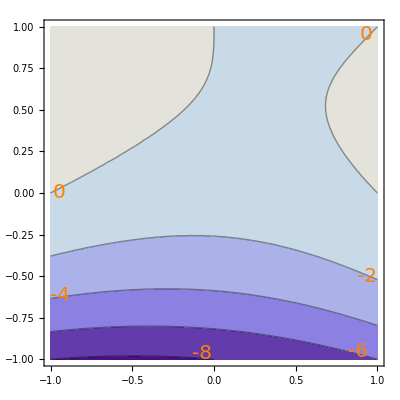

```mathematica
ContourPlot[x^2-x y + (y-1)^3,{x,-1,1},{y,-1,1},ContourLabels->(Text[Style[#3,Orange,FontSize->20],{.95 #1,.97#2}]&)]
```

## Three-Dimensional Surface Plots

Plot3D[f,{x,xmin,xmax},{y,ymin,ymax}] | make a three-dimensional plot of f as a function of the variables x and y

Basic 3D plotting function.

## Plotting Lists of Data

ListPlot[{y_1,y_2,...}]  | plot y_1, y_2, ... at x values 1, 2, ... 
ListPlot[{{x_1,y_1},{x_(2,)y_2},...}]  | plot points (x_1,y_1), ...
ListPlot[list, Joined→True] | join the points with lines 
ListPlot[{list_1, list_2}]  | plot two lists of data at once
ListPlot[{{z_11,z_12,...},{z_(21,)z_22,...},...}]  | make a three-dimensional plot of the array of heights z_yx
ListContourPlot[array]  | make a contour plot from an array of heights
ListDensityPlot[array]  | make a density plot

Functions for plotting lists of data.

To create your own data  markers and add text to a plot:

```mathematica
Graphics[{Red,Disk[{0,0},1]}]
```

-Graphics-

The size of the disk was reduced. Now it can be pasted into a PlotMarkers option. Text can also be used as a data marker.

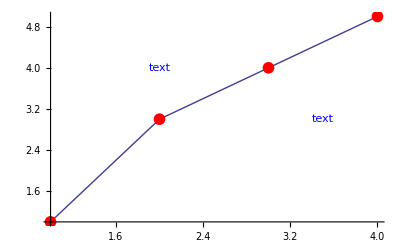

```mathematica
ListPlot[{{1,3,4,5},{{2,4},{3.5,3}}},Joined->{True,False},PlotMarkers->{"","text"}]
```

## Parametric Plots

ParametricPlot[{f_x,f_y},{t,tmin,tmax}] | make a parametric plot 
ParametricPlot[{{f_x,f_y},{g_x,g_y},...},{t,tmin,tmax}] | plot several parametric curves together
ParametricPlot[{f_x,f_y},{t,tmin,tmax},AspectRatio->Automatic] | attempt to preserve the shapes of curves

Functions for generating parametric plots.

ParametricPlot3D[{f_x,f_y,f_z},{t,tmin,tmax}] | make a parametric plot of a three-dimensional curve
ParametricPlot3D[{f_x,f_y,f_z}, {s,smin,smax},{t,tmin,tmax}] | make a parametric plot of a three-dimensional surface
ParametricPlot3D[{{f_x,f_y,f_z},{g_x,g_y,g_z},...}{t,tmin,tmax}] | plot several objects together

Three-dimensional parametric plots.

## Some Other Plots

<<add-on package` | load an add-on  package for setting up some additional  functions
LogPlot[f,{x,xmin,xmax}]  | generate a log-linear plot 
LogLogPlot[f,{x,xmin,xmax}]  | generate a log-log plot
ListLogPlot[list]  | generate a log-log plot from a list of data 
ListLogLogPlot[list]  | generate a log-log plot from a list of data
PolarPlot[r,{θ,θmin,θmax}]   | generate a polar plot of the radius r as a function of angle θ
ErrorListPlot[{{x_1,y_1, dy_1},...}]  | generate a plot of data with error bars. Requires the ErrorBarPlots add-on package.
BarChart[list] | plot a list of data as a bar chart
PieChart[list] | plot a list of data as a pie chart
VectorPlot[{f_x,f_y}, {x,xmin,xmax},{y,ymin,ymax}]  | plot the vector field corresponding to the vector function {f_x,f_y}
ListVectorPlot[list] | plot the vector field corresponding to the two-dimensional array of vectors in  list
SphericalPlot3D[r,{θ,θmin,θmax},{ϕ,ϕmin,ϕmax}]   | generate a three-dimensional spherical plot

Some special plotting functions defined in standard Mathematica packages.

9.12.5 Dynamic Content

Dynamic[x] | create a variable that is updated automatically everywhere it appears, whenever it is changed
Slider[Dynamic[x]] | create a slider that updates a  dynamic variable
Manipulate[expression, parameter] | create a dynamic expression in which a parameter can be  updated via a slider and other controls
Animate[expression,{parameter,min,max}] | a type of dynamic expression where the parameter is updated automatically, looping between the given min and max values
ListAnimate[list] | loops over the elements of the list, displaying each consecutively
DynamicModule[{local vars}, dynamic content] | isolates local variables used in dynamic content so that their values do not affect the Global context; values are remembered from session to session.

An example of the use of a dynamic module:

```mathematica
DynamicModule[{y},{Dynamic[y+10^y], Slider[Dynamic[y]]}]
```

The value of the variable y is local to the module. Its value is remembered from kernel session to kernel session.

```mathematica
?y
```

Global`y

9.12.6 Symbolic Mathematics

## General Definitions

f[x_] = x^2 | define a function f
?f | show the definition of f
Clear[f] | clear the definition of f
Remove[f] | clear the definition of f and remove it from the list of user-defined symbols

Defining a function.

f[x], f@x, x//f | all mean  evaluate the function f at x
f[x,y],x~f~y | evaluate a function of 2 variables at x and y

Different ways to evaluate functions.

D[f,x] | (partial) derivative of f with respect to x
Integrate[f,x] | indefinite integral of f with respect to x
Integrate[f,{x,a,b}] | definite integral of f with respect to x from a to b
Sum[f,{i,imin,imax}] | the sum  ∑_(i=imin)^imax f
Solve[lhs==rhs,x] | solution to an equation for x
Series[f,{x,x_0,order}] | series expansion of f about the point x_0
Normal[series] | normal Mathematica expression derived from a series expression
Limit[f,x→x_0] | limit of f as x approaches x_0

Some symbolic mathematical operations.

## Algebraic Equations

x=y | immediately evaluates y and assigns the result to x
x:=y | assigns y to x without evaluating y immediately
x==y | tests whether x and y are equal

Three types of equal signs

x==y | equal
x!=y | unequal
x>y | greater than
x>=y | greater than or equal to
x<y | less than
x<=y | less than or equal to
x∈y | x is an element of the set y
statement 1 || statement 2 | either statement 1 or statement 2 is true
statement 1 && statement 2 | both statement 1 and statement 2 are true

Logical statements

Solve[lhs==rhs,x] | solve an equation, giving a list of replacement rules for x
x/.solution | use the list of rules to get values for x
expr/.solution | use the list of rules to get values for an expression

Finding and using solutions to equations.

```mathematica
Solve[{x^2 + y^2 ==2,y+x-1==0},{x,y}]
```

{{x→1/2 (1-√3),y→1/2 (1+√3)},{x→1/2 (1+√3),y→1/2 (1-√3)}}

## Differential Equations

DSolve[eqn, y(x),x] | solve a differential equation for y(x)

DSolve[{eqn_1,eqn_2,...},{y_1,y_2,...},x""] | solve a list of differential equations for functions y_1, y_2,...

Solving ordinary differential equations analytically.

```mathematica
DSolve[y''[x]+ 3 y[x]==0,y[x],x]
```

{{y[x]→C[1] Cos[√3 x]+C[2] Sin[√3 x]}}

```mathematica
DSolve[{y''[x]+ 3 y[x]==0,y[0]==2,y'[0]==0},y[x],x]
```

{{y[x]→2 Cos[√3 x]}}

NDSolve[{eqn_1,eqn_2,...},  y ,{x,xmin,xmax}] | find a numerical solution for the function y with x in the range xmin to xmax

Finding numerical solutions to ordinary differential equations.

```mathematica
NDSolve[ {y''[x]+Re[x^(1/3)] y[x]==0,y[0]==0,y'[0]==1},y[x],{x,-20,20}]
```

{{y[x]→InterpolatingFunction[{{-20.,20.}},<>][x]}}

```mathematica
y[x]/.%[[1]]
```

InterpolatingFunction[{{-20.,20.}},<>][x]

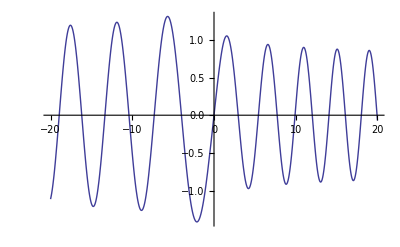

```mathematica
Plot[%,{x,-20,20}]
```

9.12.7 WolframAlpha

WolframAlpha["query"] 
             or 
          = query | 
sends  query to WolframAlpha and imports the result

Accessing the WolframAlpha computational knowledge engine

```mathematica
WolframAlpha["find the roots of x^3 +3x + 4"]
```

WolframAlphaQueryResults

WolframAlphaQueryResults

1.27 million  (2009 estimate)

## References

Samuel D. Conte and Carl de Boor, Elementary Numerical Analysis, 3rd ed. (McGraw-Hill, New York, 1980).
Stephen Wolfram, The Mathematica Book, 4th ed.  (Cambridge University Press, Cambridge, 1999).